# Plots

## Plot Style

```mathematica
<<MaTeX`;
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

### Plot style

#### Colors

```mathematica
thsize=0.004;
lgy={RGBColor[0.2,0.2,0.2],Thickness[thsize]};
lgyfill=RGBColor[0.85,0.85,0.85];
dgy={RGBColor[0,0,0],Thickness[thsize]};
dgyfill=RGBColor[0.5,0.5,0.5];
gr={RGBColor[0,0.65,0],Thickness[thsize]};
grfill=RGBColor[0.35,1,0.35];
grth={RGBColor[0,0.65,0],Thickness[0.004]};
bl={RGBColor[0,0,1],Thickness[thsize]};
blfill=RGBColor[0.5,0.7,1];
blth={RGBColor[0,0,1],Thickness[0.004]};
or={RGBColor[2,0.1,0],Thickness[thsize]};
orfill=RGBColor[1,0.5,0];
orth={RGBColor[2,0.1,0],Thickness[0.004]};
whfill=RGBColor[1,1,1];
white={RGBColor[1,1,1],Thickness[0.004]};
pur={RGBColor[0.5,0,0.5],Thickness[thsize]};
purfill=RGBColor[1,0.5,1];
mag={RGBColor[1,0,1],Thickness[thsize]};
blor1={RGBColor[0.33,0.033,0.66],Thickness[thsize]};
blor2={RGBColor[0.66,0.066,0.33],Thickness[thsize]};
```

#### Dashing

```mathematica
dashed=Dashing[{0.025,0.02}];
dotted=Dashing[{0,0.02}];
dotdashed=Dashing[{0.015,0.02,0,0.02}];
```

#### Font magnification

```mathematica
magt=1.75;
magl=1.9;
```

#### Frame thickness

```mathematica
SetOptions[Plot,FrameStyle->Thickness[0.002]]
```

{AlignmentPoint→Center,AspectRatio→1/ϕ,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→Thickness[0.002],FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

#### Ticks

```mathematica
bigl={0.025,0};
smalll={0.0125,0};

wtick[xmin_,xmax_,xbig_,xsmall_]:=
Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x,Style[""MaTeX[ToString[N[x]]],Magnification->magt],bigl},{x," ",smalll}]],{i,0,xbig xsmall}];

wtickint[xmin_,xmax_,xbig_,xsmall_]:=
Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x,Style[""MaTeX[ToString[x]],Magnification->magt],bigl},{x," ",smalll}]],{i,0,xbig xsmall}];

wtick[xmin_,xmax_,xbig_,xsmall_,padn_,padf_]:=
Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x,Style[PaddedForm[x,{padn,padf}],Magnification->magt],bigl},{x," ",smalll}]],{i,0,xbig xsmall}];

wticknn[xmin_,xmax_,xbig_,xsmall_]:=
Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x," ",bigl},{x," ",smalll}]],{i,0,xbig xsmall}];

Logwtick[xmin_,xmax_,xbig_,xsmall_]:=Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x,Style[""MaTeX[Superscript[10,Round[Log10[x]]]],Magnification->magt],bigl},{x," ",smalll}]],{i,0,xbig xsmall}];


Logwticknn[xmin_,xmax_,xbig_,xsmall_]:=
Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x," ",bigl},{x," ",smalll}]],{i,0,xbig xsmall}];
```

#### Legend

```mathematica
boxsize=0.1;
boxratio=4/3;
cutedge=0.02;
legbox[x_,y_,col_,fill_,boxt_,xmin_,xmax_,ymin_,ymax_]:=
{{fill,Rectangle[{x,y},{x+boxsize(xmax-xmin),y+boxsize(ymax-ymin)/boxratio}]},Join[col,{Line[{{x+cutedge boxsize(xmax-xmin),y+boxsize(ymax-ymin)/boxratio/2},{x+(1-cutedge)boxsize(xmax-xmin),y+boxsize(ymax-ymin)/boxratio/2}}]}],Text[Style[boxt,Magnification->magl],{x+1.2 boxsize(xmax-xmin),y+boxsize(ymax-ymin)/boxratio/2},{-1,0}]}

textbox[x_,y_,boxt_,xmin_,xmax_,ymin_,ymax_]:=
{Text[Style[boxt,FontFamily->Times,Magnification->magl],{x,y},{-1,0}]}
```

```mathematica
legdata[x_,y_,sc_]:={Rectangle[Offset[{-3sc,-3sc},{x,y}],Offset[{3sc,3sc},{x,y}]],
Line[{Offset[{0,-8sc},{x,y}],Offset[{0,8sc},{x,y}]}],
Line[{Offset[{-1.5sc,-8sc},{x,y}],Offset[{1.5sc,-8sc},{x,y}]}],
Line[{Offset[{-1.5sc,8sc},{x,y}],Offset[{1.5sc,8sc},{x,y}]}]};
```

## Plots

```mathematica
ResourceFunction["DarkMode"][False]
```

```mathematica
(*
ConfigureMaTeX["pdfLaTeX"->"C:\\Users\\Kyle\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.02.0\\bin\\gswin64c.exe"]
*)
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\Users\Kyle\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.02.0\bin\gswin64c.exe}

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
epJ0p25=Import["./analysis/ep_10_100_K0_density_pow025/3d_hists.csv","Data","FieldSeparators"->","];
epJ0p5=Import["./analysis/ep_10_100_K0_density_pow05/3d_hists.csv","Data","FieldSeparators"->","];
epJ1=Import["./analysis/ep_10_100_K0_density_pow1/3d_hists.csv","Data","FieldSeparators"->","];
epJ1p5=Import["./analysis/ep_10_100_K0_density_pow15/3d_hists.csv","Data","FieldSeparators"->","];

eCJ0p25=Import["./analysis/eC_10_100_K4_density_pow025/3d_hists.csv","Data","FieldSeparators"->","];
eCJ0p5=Import["./analysis/eC_10_100_K4_density_pow05/3d_hists.csv","Data","FieldSeparators"->","];
eCJ1=Import["./analysis/eC_10_100_K4_density_pow1/3d_hists.csv","Data","FieldSeparators"->","];
eCJ1p5=Import["./analysis/eC_10_100_K4_density_pow15/3d_hists.csv","Data","FieldSeparators"->","];

eAuK0p01J0p5 = Import["./analysis/eAu_10_100_K0p01_density_pow05/3d_hists.csv","Data","FieldSeparators"->","];
eAuK0p01J1 = Import["./analysis/eAu_10_100_K0p01_density_pow1/3d_hists.csv","Data","FieldSeparators"->","];
eAuK0p01J1p5 = Import["./analysis/eAu_10_100_K0p01_density_pow15/3d_hists.csv","Data","FieldSeparators"->","];

eAuK0p1J0p5 = Import["./analysis/eAu_10_100_K0p1_density_pow05/3d_hists.csv","Data","FieldSeparators"->","];
eAuK0p1J1 = Import["./analysis/eAu_10_100_K0p1_density_pow1/3d_hists.csv","Data","FieldSeparators"->","];
eAuK0p1J1p5 = Import["./analysis/eAu_10_100_K0p1_density_pow15/3d_hists.csv","Data","FieldSeparators"->","];

eAuK2J0p5 = Import["./analysis/eAu_10_100_K2_density_pow05/3d_hists.csv","Data","FieldSeparators"->","];
eAuK2J1p5 = Import["./analysis/eAu_10_100_K2_density_pow15/3d_hists.csv","Data","FieldSeparators"->","];

eAuK100J0p5 = Import["./analysis/eAu_10_100_K100_density_pow05/3d_hists.csv","Data","FieldSeparators"->","];
eAuK100J1 = Import["./analysis/eAu_10_100_K100_density_pow1/3d_hists.csv","Data","FieldSeparators"->","];
eAuK100J1p5 = Import["./analysis/eAu_10_100_K100_density_pow15/3d_hists.csv","Data","FieldSeparators"->","];

eAuJ0p25=Import["./analysis/eAu_10_100_K4_density_pow025/3d_hists.csv","Data","FieldSeparators"->","];
eAuJ0p5=Import["./analysis/eAu_10_100_K4_density_pow05/3d_hists.csv","Data","FieldSeparators"->","];
eAuJ1=Import["./analysis/eAu_10_100_K4_density_pow1/3d_hists.csv","Data","FieldSeparators"->","];
eAuJ1p5=Import["./analysis/eAu_10_100_K4_density_pow15/3d_hists.csv","Data","FieldSeparators"->","];

(*eAuJ0p25colonly=Import["./analysis/eAu_10_100_K4_density_norad_pow025/3d_hists.csv","Data","FieldSeparators"->","];*)
eAuJ1colonly=Import["./analysis/eAu_10_100_K4_density_norad_pow1/3d_hists.csv","Data","FieldSeparators"->","];

eUJ0p25=Import["./analysis/eU_10_100_K4_density_pow025/3d_hists.csv","Data","FieldSeparators"->","];
eUJ0p5=Import["./analysis/eU_10_100_K4_density_pow05/3d_hists.csv","Data","FieldSeparators"->","];
eUJ1=Import["./analysis/eU_10_100_K4_density_pow1/3d_hists.csv","Data","FieldSeparators"->","];
eUJ1p5=Import["./analysis/eU_10_100_K4_density_pow15/3d_hists.csv","Data","FieldSeparators"->","];
```

```mathematica
Length[eAuJ0p25]
```

```mathematica
5000
```

5000

```mathematica
rlselection = 4901 (* 4853 *)
```

4901

### e+p definitions

```mathematica
Length[epJ0p25]

epJ0p25t=Select[epJ0p25,#[[1]]==epJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
epJ0p25tt=Map[{#[[1]],#[[2]],(#[[3]])/(epJ0p25t[[1]][[3]])}&,epJ0p25t];

epJ0p5t=Select[epJ0p5,#[[1]]==epJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
epJ0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(epJ0p5t[[1]][[3]])}&,epJ0p5t];

epJ1t=Select[epJ1,#[[1]]==epJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
epJ1tt=Map[{#[[1]],#[[2]],(#[[3]])/(epJ1t[[1]][[3]])}&,epJ1t];

epJ1p5t=Select[epJ1p5,#[[1]]==epJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
epJ1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(epJ1p5t[[1]][[3]])}&,epJ1p5t];

(* Integral definition for normalization in the next few steps *)
integrateData[data_]:=
Module[{xlow,xhigh,ylow,yhigh},
xlow=0; (* xi *)
xhigh=0.3;
ylow=0; (* phi *)
yhigh=0.5;
Total[Select[data,xlow<#[[1]]<xhigh&&ylow<#[[2]]<yhigh&][[All,3]]]];

normalizeData[data_,baseline_]:=
Module[{scalingFactor},
scalingFactor=integrateData[baseline]/integrateData[data];
Map[{#[[1]],#[[2]],#[[3]]*scalingFactor}&,data]];

integrateDataRange[data_,xhigh_,yhigh_]:=
Module[{xlow,ylow},
xlow=0; (* xi *)
ylow=0; (* phi *)
Total[Select[data,xlow<#[[1]]<xhigh&&ylow<#[[2]]<yhigh&][[All,3]]]];

normalizeDataRange[data_,baseline_,xhigh_,yhigh_]:=
Module[{scalingFactor},
scalingFactor=integrateDataRange[baseline,xhigh,yhigh]/integrateDataRange[data,xhigh,yhigh];
Map[{#[[1]],#[[2]],#[[3]]*scalingFactor}&,data]];
```

5000

### e+C definitions

```mathematica
Length[eCJ0p25]

eCJ0p25t=Select[eCJ0p25,#[[1]]==eCJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eCJ0p25tt=Map[{#[[1]],#[[2]],(#[[3]])/(eCJ0p25t[[1]][[3]])}&,eCJ0p25t];
eCJ0p25tt=normalizeData[eCJ0p25tt, epJ0p25tt];

eCJ0p5t=Select[eCJ0p5,#[[1]]==eCJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eCJ0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eCJ0p5t[[1]][[3]])}&,eCJ0p5t];
eCJ0p5tt=normalizeData[eCJ0p5tt, epJ0p5tt];

eCJ1t=Select[eCJ1,#[[1]]==eCJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eCJ1tt=Map[{#[[1]],#[[2]],(#[[3]])/(eCJ1t[[1]][[3]])}&,eCJ1t];
eCJ1tt=normalizeData[eCJ1tt, epJ1tt];

eCJ1p5t=Select[eCJ1p5,#[[1]]==eCJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eCJ1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eCJ1p5t[[1]][[3]])}&,eCJ1p5t];
eCJ1p5tt=normalizeData[eCJ1p5tt, epJ1p5tt];
```

5000

### e+Au definitions

```mathematica
Length[eAuJ0p25]

eAuJ0p25t=Select[eAuJ0p25,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuJ0p25tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuJ0p25t[[1]][[3]])}&,eAuJ0p25t];
eAuJ0p25tt=normalizeData[eAuJ0p25tt, epJ0p25tt];

ListPlot3D[{epJ0p25tt,eAuJ0p25tt}]


eAuJ0p5t=Select[eAuJ0p5,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuJ0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuJ0p5t[[1]][[3]])}&,eAuJ0p5t];
eAuJ0p5tt=normalizeData[eAuJ0p5tt, epJ0p5tt];
eAuJ1t=Select[eAuJ1,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuJ1tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuJ1t[[1]][[3]])}&,eAuJ1t];
eAuJ1tt=normalizeData[eAuJ1tt, epJ1tt];
eAuJ1p5t=Select[eAuJ1p5,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuJ1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuJ1p5t[[1]][[3]])}&,eAuJ1p5t];
eAuJ1p5tt=normalizeData[eAuJ1p5tt, epJ1p5tt];

Length[eAuK0p01J0p05]

eAuK0p01J0p5t=Select[eAuK0p01J0p5,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuK0p01J0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuK0p01J0p5t[[1]][[3]])}&,eAuK0p01J0p5t];
eAuK0p01J0p5tt=normalizeData[eAuK0p01J0p5tt, epJ0p5tt];
eAuK0p01J1t=Select[eAuK0p01J1,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuK0p01J1tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuK0p01J1t[[1]][[3]])}&,eAuK0p01J1t];
eAuK0p01J1tt=normalizeData[eAuK0p01J1tt, epJ1tt];
eAuK0p01J1p5t=Select[eAuK0p01J1p5,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuK0p01J1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuK0p01J1p5t[[1]][[3]])}&,eAuK0p01J1p5t];
eAuK0p01J1p5tt=normalizeData[eAuK0p01J1p5tt, epJ1p5tt];


eAuK0p1J0p5t=Select[eAuK0p1J0p5,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuK0p1J0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuK0p1J0p5t[[1]][[3]])}&,eAuK0p1J0p5t];
eAuK0p1J0p5tt=normalizeData[eAuK0p1J0p5tt, epJ0p5tt];
eAuK0p1J1t=Select[eAuK0p1J1,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuK0p1J1tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuK0p1J1t[[1]][[3]])}&,eAuK0p1J1t];
eAuK0p1J1tt=normalizeData[eAuK0p1J1tt, epJ1tt];
eAuK0p1J1p5t=Select[eAuK0p1J1p5,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuK0p1J1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuK0p1J1p5t[[1]][[3]])}&,eAuK0p1J1p5t];
eAuK0p1J1p5tt=normalizeData[eAuK0p1J1p5tt, epJ1p5tt];


eAuK2J0p5t=Select[eAuK2J0p5,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuK2J0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuK2J0p5t[[1]][[3]])}&,eAuK2J0p5t];
eAuK2J0p5tt=normalizeData[eAuK2J0p5tt, epJ0p5tt];
eAuK2J1p5t=Select[eAuK2J1p5,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuK2J1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuK2J1p5t[[1]][[3]])}&,eAuK2J1p5t];
eAuK2J1p5tt=normalizeData[eAuK2J1p5tt, epJ1p5tt];


eAuK100J0p5t=Select[eAuK100J0p5,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuK100J0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuK100J0p5t[[1]][[3]])}&,eAuK100J0p5t];
eAuK100J0p5tt=normalizeData[eAuK100J0p5tt, epJ0p5tt];
eAuK100J1t=Select[eAuK100J1,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuK100J1tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuK100J1t[[1]][[3]])}&,eAuK100J1t];
eAuK100J1tt=normalizeData[eAuK100J1tt, epJ1tt];
eAuK100J1p5t=Select[eAuK100J1p5,#[[1]]==eAuJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eAuK100J1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuK100J1p5t[[1]][[3]])}&,eAuK100J1p5t];
eAuK100J1p5tt=normalizeData[eAuK100J1p5tt, epJ1p5tt];
```

5000

-Graphics3D-

0

### e+U definitions

```mathematica
Length[eUJ0p25]

eUJ0p25t=Select[eUJ0p25,#[[1]]==eUJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eUJ0p25tt=Map[{#[[1]],#[[2]],(#[[3]])/(eUJ0p25t[[1]][[3]])}&,eUJ0p25t];
eUJ0p25tt=normalizeData[eUJ0p25tt, epJ0p25tt];

eUJ0p5t=Select[eUJ0p5,#[[1]]==eUJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eUJ0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eUJ0p5t[[1]][[3]])}&,eUJ0p5t];
eUJ0p5tt=normalizeData[eUJ0p5tt, epJ0p5tt];

eUJ1t=Select[eUJ1,#[[1]]==eUJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eUJ1tt=Map[{#[[1]],#[[2]],(#[[3]])/(eUJ1t[[1]][[3]])}&,eUJ1t];
eUJ1tt=normalizeData[eUJ1tt, epJ1tt];

eUJ1p5t=Select[eUJ1p5,#[[1]]==eUJ0p5[[rlselection]][[1]] &][[;;,{3,5,7}]];
eUJ1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eUJ1p5t[[1]][[3]])}&,eUJ1p5t];
eUJ1p5tt=normalizeData[eUJ1p5tt, epJ1p5tt];
```

5000

### xi-phi plane triangle graphic

```mathematica
upperright = {{.73,1-0.26,0},{.93,1-0.26,0},{.830,1-0.12, 0}};
uppermiddle = {{.4,1-0.26,0},{.58,1-0.26,0},{.45,1-0.11, 0}};
upperleft = {{.05,1-0.26,0},{.26,1-0.26,0},{.05,1-0.10, 0}};
midleft = {{.05,1-0.57,0},{.26,1-0.57,0},{.05,(0.26-0.09)/2 +1-0.57, 0}};
midmiddle = {{.4,1-0.57,0},{.58,1-0.57,0},{.45,(0.26-0.09)/2 +1-0.57, 0}};
midright = {{.73,1-0.57,0},{.93,1-0.57,0},{.830,(0.26-0.09)/2 +1-0.57, 0}};
lowright = {{.73,1-0.83,0},{.93,1-0.83,0},{.830,1-0.83, 0}};
lowmiddle = {{.4,1-0.83,0},{.58,1-0.83,0},{.45,1-0.83, 0}};
lowleft = {{.05,1-0.83,0},{.26,1-0.83,0},{.08,1-0.83, 0}};

yscale = Pi/2;
upperright = Map[{#[[1]],#[[2]]*yscale,#[[3]]}&,upperright];
uppermiddle = Map[{#[[1]],#[[2]]*yscale,#[[3]]}&,uppermiddle];
upperleft = Map[{#[[1]],#[[2]]*yscale,#[[3]]}&,upperleft];
midright = Map[{#[[1]],#[[2]]*yscale,#[[3]]}&,midright];
midmiddle = Map[{#[[1]],#[[2]]*yscale,#[[3]]}&,midmiddle];
midleft = Map[{#[[1]],#[[2]]*yscale,#[[3]]}&,midleft];
lowright = Map[{#[[1]],#[[2]]*yscale,#[[3]]}&,lowright];
lowmiddle = Map[{#[[1]],#[[2]]*yscale,#[[3]]}&,lowmiddle];
lowleft = Map[{#[[1]],#[[2]]*yscale,#[[3]]}&,lowleft];

allverticies =Join[upperleft,uppermiddle,upperright,midleft,midmiddle,midright,lowright,lowmiddle,lowleft];

magl=1.4;

gridx=Range[0,1,0.1];
gridy=Range[0,Pi/2,Pi*0.1/2];

trianglePlot=Graphics3D[{EdgeForm[Thick],FaceForm[None],Polygon[upperright],Polygon[uppermiddle],Polygon[upperleft], Polygon[midleft], Polygon[midmiddle], Polygon[midright], Polygon[lowright],Polygon[lowmiddle],Polygon[lowleft],FaceForm[Red],
Sphere[allverticies,0.017]}, PlotRange->{{0,1},{0,Pi/2},Automatic}, FaceGrids->{{{0,0,1},{gridx,gridy}}},Boxed->False,BoxStyle->Directive[Opacity[0]],BoxRatios->{1,1,0.01}];

Show[trianglePlot,Axes->{True, True, False},PlotRange->Automatic,AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->1.5*magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->1.5*magl], ""},ImageSize->Large]
```

-Graphics3D-

```mathematica
zbox=0.7;
magl=1.4;

plotview={ViewPoint->{2,1,0.5},AxesEdge->{{1,-1},{1,-1},{1,-1}}};

plotnucJ0p25=ListPlot3D[{epJ0p25tt, eCJ0p25tt, eAuJ0p25tt}, PlotStyle -> Opacity[0.75],PlotLegends->SwatchLegend[{Style[MaTeX["e+p"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl],Style[MaTeX["e+C"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl],Style[MaTeX["e+Au"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl]}]];

Show[trianglePlot,plotnucJ0p25,PlotRange->{{0,1},{0,Pi/2},{0,7}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->1*magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->1*magl], Style[MaTeX["\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle",Magnification->1*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 0.25",FontSize->30],plotview]

plotnucJ0p25=ListPlot3D[{epJ0p25tt, eCJ0p25tt, eAuJ0p25tt}, PlotStyle -> Opacity[0.75]];
plotnucJ0p5= ListPlot3D[{epJ0p5tt, eCJ0p5tt, eAuJ0p5tt}, PlotStyle -> Opacity[0.75]];
plotnucJ1 = ListPlot3D[{epJ1tt, eCJ1tt, eAuJ1tt}, PlotStyle -> Opacity[0.75]];
plotnucJ1p5 = ListPlot3D[{epJ1p5tt, eCJ1p5tt, eAuJ1p5tt}, PlotStyle -> Opacity[0.75]];

Show[trianglePlot,plotnucJ0p25,PlotRange->{{0,1},{0,Pi/2},{0,7}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->1*magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->1*magl], Style[MaTeX["\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle",Magnification->1.3*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 0.25",FontSize->30],plotview]
Show[trianglePlot,plotnucJ0p5,PlotRange->{{0,1},{0,Pi/2},{0,7}},BoxRatios->{1,1,zbox},ImageSize->Large,ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->1*magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->1*magl], Style[MaTeX["\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle",Magnification->1.3*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 0.5",FontSize->30],plotview]
Show[trianglePlot,plotnucJ1,PlotRange->{{0,1},{0,Pi/2},{0,7}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->1*magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->1*magl], Style[MaTeX["\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle",Magnification->1.3*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 1",FontSize->30],plotview]
Show[trianglePlot,plotnucJ1p5,PlotRange->{{0,1},{0,Pi/2},{0,7}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->1*magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->1*magl], Style[MaTeX["\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle",Magnification->1.3*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 1.5",FontSize->30],plotview]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

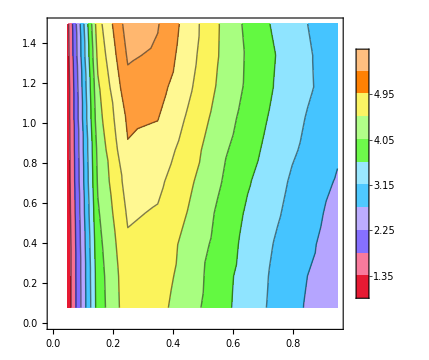

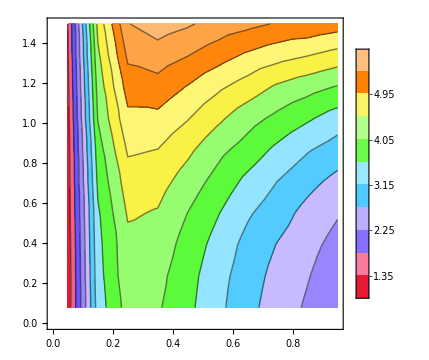

```mathematica
ListContourPlot[epJ1tt, Contours->20, ColorFunction->"BrightBands", ImageSize->Medium, PlotLegends->BarLegend[{Automatic,{1,6}}, 10],PlotRange->{1,6},FrameLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl]},PlotLabel->MaTeX["e+p, J = 1",FontSize->24]]
ListContourPlot[eAuJ1tt, Contours->20, ColorFunction->"BrightBands",ImageSize->Medium, PlotLegends->BarLegend[{Automatic,{1,6}}, 10],PlotRange->{1,6},FrameLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl]},PlotLabel->MaTeX["e+Au, J = 1",FontSize->24]]
```

```mathematica
plotKJ0p5 = ListPlot3D[{epJ0p5tt, eAuK0p01J0p5tt,eAuK0p1J0p5tt, eAuK100J0p5tt},PlotStyle->Opacity[0.75],PlotLegends->SwatchLegend[{Style[MaTeX["e+p"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl],Style[MaTeX["e+Au, K = 0.01"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl],Style[MaTeX["e+Au, K = 0.1"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl], Style[MaTeX["e+Au, K = 100"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl]}]];
Show[trianglePlot,plotKJ0p5,PlotRange->{{0,1},{0,Pi/2},{0,7}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->magl], Style[MaTeX["\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle",Magnification->magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 0.5",FontSize->30],plotview]

plotKJ0p5 = ListPlot3D[{epJ0p5tt, eAuK0p01J0p5tt,eAuK0p1J0p5tt, eAuK100J0p5tt},PlotStyle->Opacity[0.75]];
plotKJ1 = ListPlot3D[{epJ1tt, eAuK0p01J1tt,eAuK0p1J1tt, eAuK100J1tt},PlotStyle->Opacity[0.75]];
plotKJ1p5 = ListPlot3D[{epJ1p5tt, eAuK0p01J1p5tt,eAuK0p1J1p5tt, eAuK100J1p5tt},PlotStyle->Opacity[0.75]];

Show[trianglePlot,plotKJ0p5,PlotRange->{{0,1},{0,Pi/2},{0,6}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->magl], Style[MaTeX["\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle",Magnification->1.3*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 0.5",FontSize->30],plotview]
Show[trianglePlot,plotKJ1,PlotRange->{{0,1},{0,Pi/2},{0,6}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->magl], Style[MaTeX["\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle",Magnification->1.3*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 1",FontSize->30],plotview]
Show[trianglePlot,plotKJ1p5,PlotRange->{{0,1},{0,Pi/2},{0,6}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->magl], Style[MaTeX["\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle",Magnification->1.3*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 1.5",FontSize->30],plotview]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
eCJ0p25ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p25tt[[1]][[3]])/(eCJ0p25tt[[1]][[3]])}&,{eCJ0p25tt,epJ0p25tt}];
eCJ0p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p5tt[[1]][[3]])/(eCJ0p5tt[[1]][[3]])}&,{eCJ0p5tt,epJ0p5tt}];
eCJ1ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1tt[[1]][[3]])/(eCJ1tt[[1]][[3]])}&,{eCJ1tt,epJ1tt}];
eCJ1p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1p5tt[[1]][[3]])/(eCJ1p5tt[[1]][[3]])}&,{eCJ1p5tt,epJ1p5tt}];

xhigh=0.5;
yhigh=0.75;
eAuJ0p25ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p25tt[[1]][[3]])/(eAuJ0p25tt[[1]][[3]])}&,{eAuJ0p25tt,epJ0p25tt}];
eAuJ0p25ratio=normalizeDataRange[eAuJ0p25ratio,uniform,xhigh, yhigh];
eAuJ0p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p5tt[[1]][[3]])/(eAuJ0p5tt[[1]][[3]])}&,{eAuJ0p5tt,epJ0p5tt}];
eAuJ0p5ratio=normalizeDataRange[eAuJ0p5ratio,uniform,xhigh, yhigh];
eAuJ1ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1tt[[1]][[3]])/(eAuJ1tt[[1]][[3]])}&,{eAuJ1tt,epJ1tt}];
eAuJ1ratio=normalizeDataRange[eAuJ1ratio,uniform,xhigh, yhigh];
eAuJ1p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1p5tt[[1]][[3]])/(eAuJ1p5tt[[1]][[3]])}&,{eAuJ1p5tt,epJ1p5tt}];
eAuJ1p5ratio=normalizeDataRange[eAuJ1p5ratio,uniform,xhigh, yhigh];

eUJ0p25ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p25tt[[1]][[3]])/(eUJ0p25tt[[1]][[3]])}&,{eUJ0p25tt,epJ0p25tt}];
eUJ0p25ratio=normalizeDataRange[eUJ0p25ratio,uniform,xhigh, yhigh];
eUJ0p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p5tt[[1]][[3]])/(eUJ0p5tt[[1]][[3]])}&,{eUJ0p5tt,epJ0p5tt}];
eUJ0p5ratio=normalizeDataRange[eUJ0p5ratio,uniform,xhigh, yhigh];
eUJ1ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1tt[[1]][[3]])/(eUJ1tt[[1]][[3]])}&,{eUJ1tt,epJ1tt}];
eUJ1ratio=normalizeDataRange[eUJ1ratio,uniform,xhigh, yhigh];
eUJ1p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1p5tt[[1]][[3]])/(eUJ1p5tt[[1]][[3]])}&,{eUJ1p5tt,epJ1p5tt}];
eUJ1p5ratio=normalizeDataRange[eUJ1p5ratio,uniform,xhigh, yhigh];

uniform =Map[{#[[1]], #[[2]], 1}&, epJ1p5tt];
```

```mathematica
plotview={ViewPoint->{2,0,0.5},AxesEdge->{{1,-1},{1,-1},{1,-1}}};

plotratioJ0p25 = ListPlot3D[{uniform,eCJ0p25ratio,eAuJ0p25ratio, eUJ0p25ratio},PlotRange->{0.5,2},PlotStyle->Opacity[0.75],PlotLegends->SwatchLegend[{Style[MaTeX["e+p"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl],Style[MaTeX["e+C"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl],Style[MaTeX["e+Au"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl],Style[MaTeX["e+U"],FontFamily->"Latin Modern Roman",Magnification->0.7*magl]}],plotview];
Show[trianglePlot,plotratioJ0p25,PlotRange->{{0,1},{0,Pi/2},{0,2}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->magl], Style[MaTeX["\\frac{\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle_{e+A}}{\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle_{e+p}}",Magnification->magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 0.25",FontSize->30],plotview]

plotratioJ0p25 = ListPlot3D[{uniform,eCJ0p25ratio,eAuJ0p25ratio, eUJ0p25ratio},PlotRange->{0.5,2},PlotStyle->Opacity[0.75]];
plorraioJ0p5 = ListPlot3D[{uniform,eCJ0p5ratio,eAuJ0p25ratio, eUJ0p5ratio},PlotRange->{0.5,2},PlotStyle->Opacity[0.75]];
plotratioJ1 =ListPlot3D[{uniform,eCJ1ratio,eAuJ0p25ratio, eUJ1ratio},PlotRange->{0.5,2},PlotStyle->Opacity[0.75]];
plotratioJ1p5=ListPlot3D[{uniform,eCJ1p5ratio,eAuJ0p25ratio, eUJ1p5ratio},PlotRange->{0.5,2},PlotStyle->Opacity[0.75]];

Show[trianglePlot,plotratioJ0p25,PlotRange->{{0,1},{0,Pi/2},{0,2}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->magl], Style[MaTeX["\\frac{\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle_{e+A}}{\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle_{e+p}}",Magnification->1.3*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 0.25",FontSize->30], plotview]
Show[trianglePlot,plorraioJ0p5,PlotRange->{{0,1},{0,Pi/2},{0,2}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->magl], Style[MaTeX["\\frac{\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle_{e+A}}{\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle_{e+p}}",Magnification->1.3*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 0.5",FontSize->30],plotview]
Show[trianglePlot,plotratioJ1,PlotRange->{{0,1},{0,Pi/2},{0,2}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->magl], Style[MaTeX["\\frac{\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle_{e+A}}{\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle_{e+p}}",Magnification->1.3*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 1",FontSize->30],plotview]
Show[trianglePlot,plotratioJ1p5,PlotRange->{{0,1},{0,Pi/2},{0,2}},BoxRatios->{1,1,zbox},ImageSize->Large, Axes->{True,True,True}, AxesLabel->{
Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->magl],
Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->magl], Style[MaTeX["\\frac{\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle_{e+A}}{\\langle\\mathcal{E}^J\\mathcal{E}^J\\mathcal{E}^J\\rangle_{e+p}}",Magnification->1.3*magl],FontFamily->"Latin Modern Roman"]},PlotLabel->MaTeX["J = 1.5",FontSize->30],plotview]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

### Slice plots

```mathematica
dkgr={RGBColor[25/255,79/255,93/255],Thickness[thsize]};
ligr={RGBColor[46/255,158/255,144/255],Thickness[thsize]};
ligrr={RGBColor[145/255,177/255,145/255],Thickness[thsize]};
sand={RGBColor[233/255,193/255,149/255],Thickness[thsize]};
thsize=0.004;
lgy={RGBColor[0.2,0.2,0.2],Thickness[thsize]};
lgyfill=RGBColor[0.85,0.85,0.85];
dgy={RGBColor[0,0,0],Thickness[thsize]};
dgyfill=RGBColor[0.5,0.5,0.5];
gr={RGBColor[0,0.65,0],Thickness[thsize]};
grfill=RGBColor[0.35,1,0.35];
grth={RGBColor[0,0.65,0],Thickness[0.004]};
bl={RGBColor[0,0,1],Thickness[thsize]};
blfill=RGBColor[0.5,0.7,1];
blth={RGBColor[0,0,1],Thickness[0.004]};
or={RGBColor[2,0.1,0],Thickness[thsize]};
orfill=RGBColor[1,0.5,0];
orth={RGBColor[2,0.1,0],Thickness[0.004]};
skbl={RGBColor[109/250,175/250,237/250],Thickness[thsize]};
whfill=RGBColor[1,1,1];
white={RGBColor[1,1,1],Thickness[0.004]};
pur={RGBColor[0.5,0,0.5],Thickness[thsize]};
purfill=RGBColor[1,0.5,1];
mag={RGBColor[1,0,1],Thickness[thsize]};
blor1={RGBColor[0.33,0.033,0.66],Thickness[thsize]};
blor2={RGBColor[0.66,0.066,0.33],Thickness[thsize]};
re={RGBColor[224/250,31/250,31/250],Thickness[thsize]};
(*lior={RGBColor[240/250,167/250,65/250],Thickness[thsize]};
dkor={RGBColor[227/250,121/250,7/250],Thickness[thsize]};*)
or={RGBColor[2,0.1,0],Thickness[thsize]};
dkor={RGBColor[255/255,150/255,113/255],Thickness[thsize]};
lior={RGBColor[255/255,199/255,95/255],Thickness[thsize]};
magl =1;
```

{{0.0785398,1.69068},{0.235619,1.72424},{0.392699,1.7413},{0.549779,1.7702},{0.706858,1.82123},{0.863938,1.86652},{1.02102,1.90933},{1.1781,1.95257},{1.33518,1.95366},{1.49226,1.93539}}

0.0785396

1.49226

{{2.×10^-7,1.69068},{0.157079,1.72424},{0.314159,1.7413},{0.471239,1.7702},{0.628318,1.82123},{0.785398,1.86652},{0.94248,1.90933},{1.09956,1.95257},{1.25664,1.95366},{1.41372,1.93539},{1.5708,1.93539}}

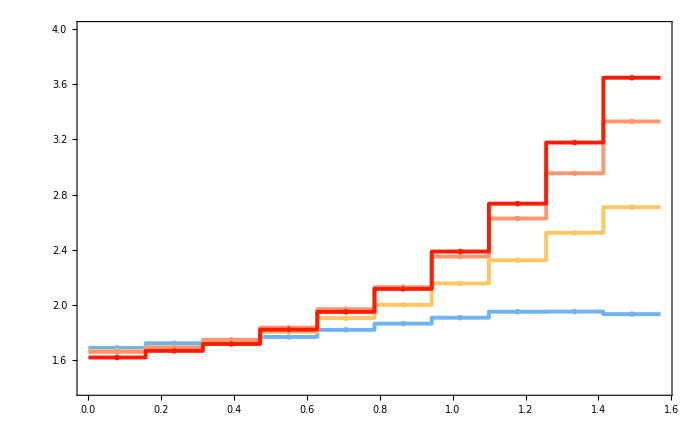

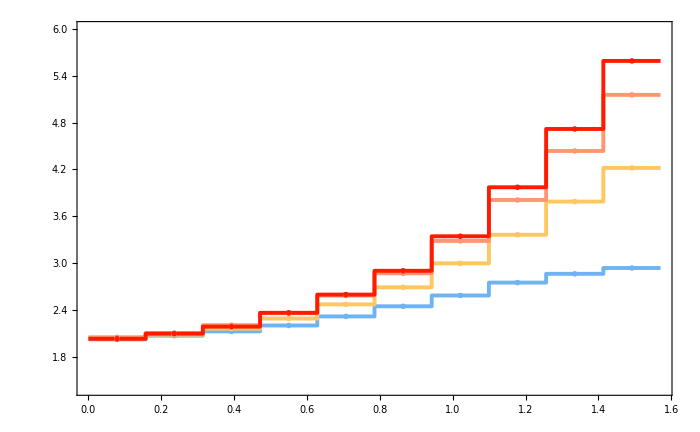

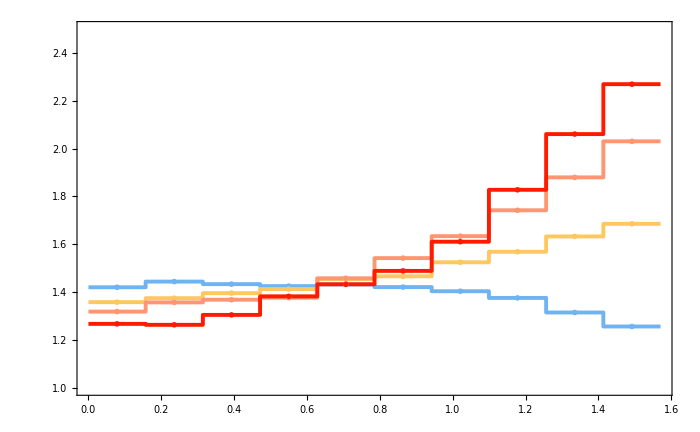

```mathematica
marker1=Graphics[{skbl[[1]],Disk[]}];
marker2=Graphics[{lior[[1]],Disk[]}];
marker3=Graphics[{dkor[[1]],Disk[]}];
marker4=Graphics[{or[[1]],Disk[]}];

xicut = 0.95;
epJ1ttxi = Select[epJ1tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK0p01J1xi = Select[eAuK0p01J1tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK0p1J1xi = Select[eAuK0p1J1tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK100J1xi = Select[eAuK100J1tt,#[[1]]==xicut&][[;;,{2,3}]];

magl=1;

epJ1ttxi=Select[epJ1tt,#[[1]]==xicut&][[;;,{2,3}]]
phiinterval=(epJ1ttxi[[2]][[1]] - epJ1ttxi[[1]][[1]])/2
highestphi=Last[epJ1ttxi][[1]]
epJ1ttximap = Join[Map[{#[[1]]-phiinterval,#[[2]]}&,epJ1ttxi], {{highestphi+phiinterval, Last[epJ1ttxi][[2]]}}]

eAuK0p01J1xi = Select[eAuK0p01J1tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK0p01J1ximap = Join[Map[{#[[1]]-phiinterval,#[[2]]}&,eAuK0p01J1xi], {{highestphi+phiinterval, Last[eAuK0p01J1xi][[2]]}}];

eAuK0p1J1xi = Select[eAuK0p1J1tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK0p1J1ximap=Join[Map[{#[[1]]-phiinterval,#[[2]]}&,eAuK0p1J1xi], {{highestphi+phiinterval, Last[eAuK0p1J1xi][[2]]}}];

eAuK100J1xi = Select[eAuK100J1tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK100J1ximap=Join[Map[{#[[1]]-phiinterval,#[[2]]}&,eAuK100J1xi], {{highestphi+phiinterval, Last[eAuK100J1xi][[2]]}}];

lines=ListPlot[{epJ1ttximap,eAuK0p01J1ximap,eAuK0p1J1ximap,eAuK100J1ximap},InterpolationOrder->0,PlotRange->{{0,highestphi+phiinterval}, {1.4,4}},Joined->True,Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},PlotStyle->{skbl,lior,dkor,or},
FrameLabel->{{Style[MaTeX["\\mathrm{E^JE^JE^J}~\\mathrm{Correlator}",Magnification->2*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->1.5*magl],None}},PlotStyle->{skbl,lior,dkor,or},  ImageSize->700,PlotLabel->MaTeX["R_L = 0.916, \\xi = 0.95 \,\,\\text{slice}, J = 1",FontSize->30],
PlotLegends->SwatchLegend[{Style[MaTeX["e+p"],Magnification->1.3*magl],Style[MaTeX["e+Au, K=0.01"],Magnification->1.3*magl],Style[MaTeX["e+Au, K=0.1"],Magnification->1.3*magl],Style[MaTeX["e+Au, K=100"],Magnification->1.3*magl]}]];
points=ListPlot[{epJ1ttxi,eAuK0p01J1xi,eAuK0p1J1xi,eAuK100J1xi}, Joined->False, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}}];
Show[lines, points]

epJ0p5ttxi=Select[epJ0p5tt,#[[1]]==xicut&][[;;,{2,3}]];
epJ0p5ttximap = Join[Map[{#[[1]]-phiinterval,#[[2]]}&,epJ0p5ttxi], {{highestphi+phiinterval, Last[epJ0p5ttxi][[2]]}}];

eAuK0p01J0p5xi = Select[eAuK0p01J0p5tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK0p01J0p5ximap = Join[Map[{#[[1]]-phiinterval,#[[2]]}&,eAuK0p01J0p5xi], {{highestphi+phiinterval, Last[eAuK0p01J0p5xi][[2]]}}];

eAuK0p1J0p5xi = Select[eAuK0p1J0p5tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK0p1J0p5ximap=Join[Map[{#[[1]]-phiinterval,#[[2]]}&,eAuK0p1J0p5xi], {{highestphi+phiinterval, Last[eAuK0p1J0p5xi][[2]]}}];

eAuK100J0p5xi = Select[eAuK100J0p5tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK100J0p5ximap=Join[Map[{#[[1]]-phiinterval,#[[2]]}&,eAuK100J0p5xi], {{highestphi+phiinterval, Last[eAuK100J0p5xi][[2]]}}];

lines=ListPlot[{epJ0p5ttximap,eAuK0p01J0p5ximap,eAuK0p1J0p5ximap,eAuK100J0p5ximap},InterpolationOrder->0,PlotRange->{{0,highestphi+phiinterval}, {1.4,6}},Joined->True,Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},PlotStyle->{skbl,lior,dkor,or},
FrameLabel->{{Style[MaTeX["\\mathrm{E^JE^JE^J}~\\mathrm{Correlator}",Magnification->2*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->1.5*magl],None}},PlotStyle->{skbl,lior,dkor,or},  ImageSize->700,PlotLabel->MaTeX["R_L = 0.916, \\xi = 0.95 \,\,\\text{slice}, J = 0.5",FontSize->30]];
points=ListPlot[{epJ0p5ttxi,eAuK0p01J0p5xi,eAuK0p1J0p5xi,eAuK100J0p5xi}, Joined->False, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}}];
Show[lines, points]

epJ1p5ttxi=Select[epJ1p5tt,#[[1]]==xicut&][[;;,{2,3}]];
epJ1p5ttximap = Join[Map[{#[[1]]-phiinterval,#[[2]]}&,epJ1p5ttxi], {{highestphi+phiinterval, Last[epJ1p5ttxi][[2]]}}];

eAuK0p01J1p5xi = Select[eAuK0p01J1p5tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK0p01J1p5ximap = Join[Map[{#[[1]]-phiinterval,#[[2]]}&,eAuK0p01J1p5xi], {{highestphi+phiinterval, Last[eAuK0p01J1p5xi][[2]]}}];

eAuK0p1J1p5xi = Select[eAuK0p1J1p5tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK0p1J1p5ximap=Join[Map[{#[[1]]-phiinterval,#[[2]]}&,eAuK0p1J1p5xi], {{highestphi+phiinterval, Last[eAuK0p1J1p5xi][[2]]}}];

eAuK100J1p5xi = Select[eAuK100J1p5tt,#[[1]]==xicut&][[;;,{2,3}]];
eAuK100J1p5ximap=Join[Map[{#[[1]]-phiinterval,#[[2]]}&,eAuK100J1p5xi], {{highestphi+phiinterval, Last[eAuK100J1p5xi][[2]]}}];

lines=ListPlot[{epJ1p5ttximap,eAuK0p01J1p5ximap,eAuK0p1J1p5ximap,eAuK100J1p5ximap},InterpolationOrder->0,PlotRange->{{0,highestphi+phiinterval}, {1,2.5}},Joined->True,Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},PlotStyle->{skbl,lior,dkor,or},
FrameLabel->{{Style[MaTeX["\\mathrm{E^JE^JE^J}~\\mathrm{Correlator}",Magnification->2*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\phi"],FontFamily->"Latin Modern Roman",Magnification->1.5*magl],None}},PlotStyle->{skbl,lior,dkor,or},  ImageSize->700,PlotLabel->MaTeX["R_L = 0.916, \\xi = 0.95 \,\,\\text{slice}, J = 1.5",FontSize->30]];
points=ListPlot[{epJ1p5ttxi,eAuK0p01J1p5xi,eAuK0p1J1p5xi,eAuK100J1p5xi}, Joined->False, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}}];
Show[lines, points]
```

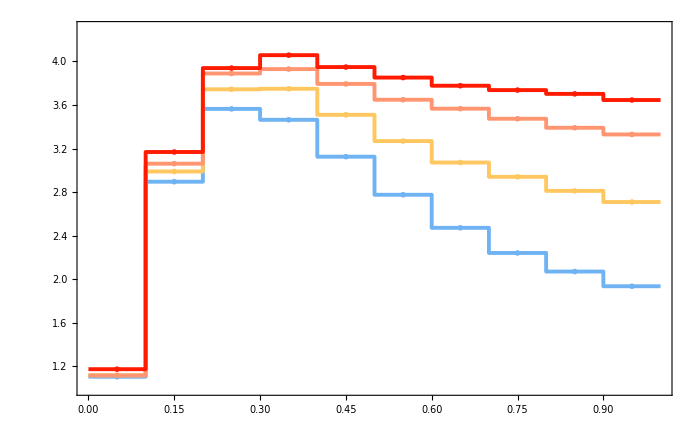

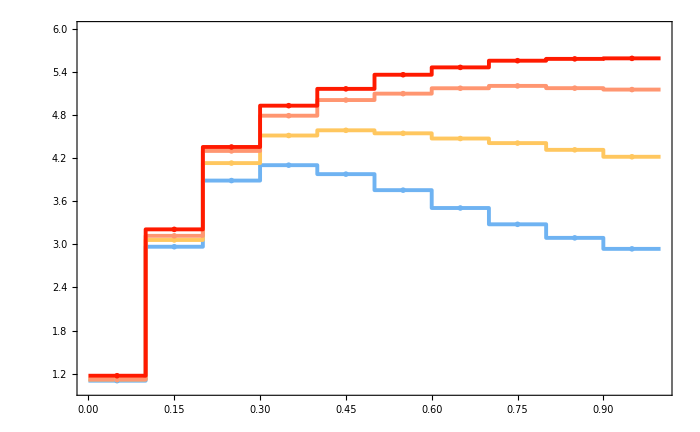

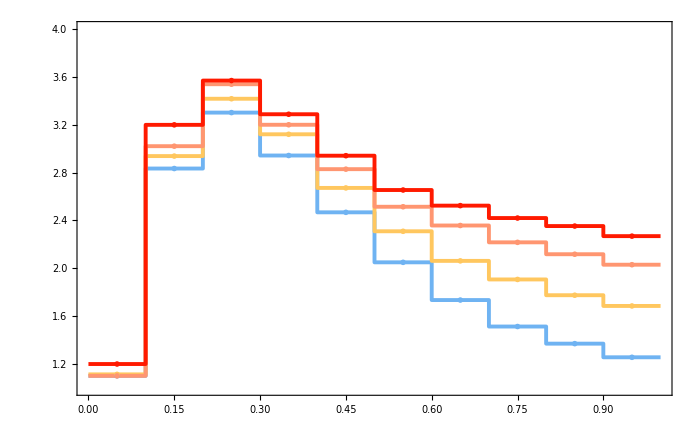

```mathematica
phicut = epJ1tt[[10]][[2]];

epJ1ttphi=Select[epJ1tt,#[[2]]==phicut&][[;;,{1,3}]];
epJ1ttphimap = Join[Map[{#[[1]]-0.05,#[[2]]}&,epJ1ttphi], {{1, Last[epJ1ttphi][[2]]}}];

eAuK0p01J1phi = Select[eAuK0p01J1tt,#[[2]]==phicut&][[;;,{1,3}]];
eAuK0p01J1phimap = Join[Map[{#[[1]]-0.05,#[[2]]}&,eAuK0p01J1phi], {{1, Last[eAuK0p01J1phi][[2]]}}];

eAuK0p1J1phi = Select[eAuK0p1J1tt,#[[2]]==phicut&][[;;,{1,3}]];
eAuK0p1J1phimap=Join[Map[{#[[1]]-0.05,#[[2]]}&,eAuK0p1J1phi], {{1, Last[eAuK0p1J1phi][[2]]}}];

eAuK100J1phi = Select[eAuK100J1tt,#[[2]]==phicut&][[;;,{1,3}]];
eAuK100J1phimap=Join[Map[{#[[1]]-0.05,#[[2]]}&,eAuK100J1phi], {{1, Last[eAuK100J1phi][[2]]}}];

lines=ListPlot[{epJ1ttphimap,eAuK0p01J1phimap,eAuK0p1J1phimap,eAuK100J1phimap},InterpolationOrder->0,PlotRange->{{0,1}, {1,4.3}},Joined->True,Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},PlotStyle->{skbl,lior,dkor,or},
FrameLabel->{{Style[MaTeX["\\mathrm{E^JE^JE^J}~\\mathrm{Correlator}",Magnification->2*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->1.5*magl],None}},PlotStyle->{skbl,lior,dkor,or},  ImageSize->700,PlotLabel->MaTeX["R_L = 0.916, \\phi = 1.5 \,\,\\text{slice}, J = 1",FontSize->30],
PlotLegends->SwatchLegend[{Style[MaTeX["e+p"],Magnification->1.3*magl],Style[MaTeX["e+Au, K=0.01"],Magnification->1.3*magl],Style[MaTeX["e+Au, K=0.1"],Magnification->1.3*magl],Style[MaTeX["e+Au, K=100"],Magnification->1.3*magl]}]];
points=ListPlot[{epJ1ttphi,eAuK0p01J1phi,eAuK0p1J1phi,eAuK100J1phi}, Joined->False, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}}];
Show[lines, points]

epJ0p5ttphi=Select[epJ0p5tt,#[[2]]==phicut&][[;;,{1,3}]];
epJ0p5ttphimap = Join[Map[{#[[1]]-0.05,#[[2]]}&,epJ0p5ttphi], {{1, Last[epJ0p5ttphi][[2]]}}];

eAuK0p01J0p5phi = Select[eAuK0p01J0p5tt,#[[2]]==phicut&][[;;,{1,3}]];
eAuK0p01J0p5phimap = Join[Map[{#[[1]]-0.05,#[[2]]}&,eAuK0p01J0p5phi], {{1, Last[eAuK0p01J0p5phi][[2]]}}];

eAuK0p1J0p5phi = Select[eAuK0p1J0p5tt,#[[2]]==phicut&][[;;,{1,3}]];
eAuK0p1J0p5phimap=Join[Map[{#[[1]]-0.05,#[[2]]}&,eAuK0p1J0p5phi], {{1, Last[eAuK0p1J0p5phi][[2]]}}];

eAuK100J0p5phi = Select[eAuK100J0p5tt,#[[2]]==phicut&][[;;,{1,3}]];
eAuK100J0p5phimap=Join[Map[{#[[1]]-0.05,#[[2]]}&,eAuK100J0p5phi], {{1, Last[eAuK100J0p5phi][[2]]}}];

lines=ListPlot[{epJ0p5ttphimap,eAuK0p01J0p5phimap,eAuK0p1J0p5phimap,eAuK100J0p5phimap},InterpolationOrder->0,PlotRange->{{0,1}, {1,6}},Joined->True,Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},PlotStyle->{skbl,lior,dkor,or},
FrameLabel->{{Style[MaTeX["\\mathrm{E^JE^JE^J}~\\mathrm{Correlator}",Magnification->2*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->1.5*magl],None}},PlotStyle->{skbl,lior,dkor,or},  ImageSize->700,PlotLabel->MaTeX["R_L = 0.916, \\phi = 1.5 \,\,\\text{slice}, J = 0.5",FontSize->30]];
points=ListPlot[{epJ0p5ttphi,eAuK0p01J0p5phi,eAuK0p1J0p5phi,eAuK100J0p5phi}, Joined->False, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}}];
Show[lines, points]

epJ1p5ttphi=Select[epJ1p5tt,#[[2]]==phicut&][[;;,{1,3}]];
epJ1p5ttphimap = Join[Map[{#[[1]]-0.05,#[[2]]}&,epJ1p5ttphi], {{1, Last[epJ1p5ttphi][[2]]}}];

eAuK0p01J1p5phi = Select[eAuK0p01J1p5tt,#[[2]]==phicut&][[;;,{1,3}]];
eAuK0p01J1p5phimap = Join[Map[{#[[1]]-0.05,#[[2]]}&,eAuK0p01J1p5phi], {{1, Last[eAuK0p01J1p5phi][[2]]}}];

eAuK0p1J1p5phi = Select[eAuK0p1J1p5tt,#[[2]]==phicut&][[;;,{1,3}]];
eAuK0p1J1p5phimap=Join[Map[{#[[1]]-0.05,#[[2]]}&,eAuK0p1J1p5phi], {{1, Last[eAuK0p1J1p5phi][[2]]}}];

eAuK100J1p5phi = Select[eAuK100J1p5tt,#[[2]]==phicut&][[;;,{1,3}]];
eAuK100J1p5phimap=Join[Map[{#[[1]]-0.05,#[[2]]}&,eAuK100J1p5phi], {{1, Last[eAuK100J1p5phi][[2]]}}];

lines=ListPlot[{epJ1p5ttphimap,eAuK0p01J1p5phimap,eAuK0p1J1p5phimap,eAuK100J1p5phimap},InterpolationOrder->0,PlotRange->{{0,1}, {1,4}},Joined->True,Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},PlotStyle->{skbl,lior,dkor,or},
FrameLabel->{{Style[MaTeX["\\mathrm{E^JE^JE^J}~\\mathrm{Correlator}",Magnification->2*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\xi"],FontFamily->"Latin Modern Roman",Magnification->1.5*magl],None}},PlotStyle->{skbl,lior,dkor,or},  ImageSize->700,PlotLabel->MaTeX["R_L = 0.916, \\phi = 1.5 \,\,\\text{slice}, J = 1.5",FontSize->30]];
points=ListPlot[{epJ1p5ttphi,eAuK0p01J1p5phi,eAuK0p1J1p5phi,eAuK100J1p5phi}, Joined->False, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}}];
Show[lines, points]
```

## EEC paper plots

```mathematica
fig2=Import["./datafiles/fig2.dat","Data","FieldSeparators"->","];
fig3=Import["./datafiles/fig3.dat","Data","FieldSeparators"->","];
fig3ReA=Import["./datafiles/fig3_ReA.dat","Data","FieldSeparators"->","];
fig4=Import["./datafiles/fig4.dat","Data","FieldSeparators"->","];
fig5=Import["./datafiles/fig5.dat","Data","FieldSeparators"->","];
fig5ReA=Import["./datafiles/fig5_ReA.dat","Data","FieldSeparators"->","];
(*fig5insert=Import["./datafiles/fig5_insert_isospin.dat","Data","FieldSeparators"->","];*)
fig5insert=Import["./datafiles/fig5_insert.dat","Data","FieldSeparators"->","];
qhatxQ=Import["./datafiles/qhat_data_Au.dat","Data","FieldSeparators"->","];
xQcoord=Table[{10^i,10^j},{j,-3,0,(0-(-3))/20},{i,0,3,(3-0)/20}];
qhatxQdata=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQ[[i]][[j]]=="nan",0,qhatxQ[[i]][[j]]]},{i,5,Length[qhatxQ]},{j,1,Length[qhatxQ[[5]]]}],1],Abs[#[[3]]]>0&];
Alist=Table[10^(fig5insert[[i]][[1]]),{i,1,Length[fig5insert]}];
```

```mathematica
fig2[[i]][[1]]-(fig2[[i]][[2]])/2
```

Part::pkspec1: The expression i cannot be used as a part specification.

```mathematica
fig2[[i]][[2]]
```

```mathematica
fig2[[i]][[1]]-(fig2[[i]][[2]])/2
```

```mathematica
f2tb[n_]:=Join[Table[{fig2[[i]][[1]]-(fig2[[i]][[2]])/2,(fig2[[i]][[2n+1]])/(fig2[[i]][[2]])},{i,1,Length[fig2]}],{{fig2[[Length[fig2]]][[1]]+(fig2[[Length[fig2]]][[2]])/2,(fig2[[Length[fig2]]][[2n+1]])/(fig2[[]][[2]])}}]
f3tb[n_]:=Join[Table[{fig3[[i]][[1]]-(fig3[[i]][[2]])/2,fig3[[i]][[2n+1]]},{i,1,Length[fig3]}],{{fig3[[Length[fig3]]][[1]]+(fig3[[Length[fig3]]][[2]])/2,fig3[[Length[fig3]]][[2n+1]]}}]
f3ReAtb[n_]:=Join[Table[{fig3ReA[[i]][[1]]-(fig3ReA[[i]][[2]])/2,fig3ReA[[i]][[2n+1]]},{i,1,Length[fig3ReA]}],{{fig3ReA[[Length[fig3ReA]]][[1]]+(fig3ReA[[Length[fig3ReA]]][[2]])/2,fig3ReA[[Length[fig3ReA]]][[2n+1]]}}]
f4tb[n_]:=Join[Table[{fig4[[i]][[1]]-(fig4[[i]][[2]])/2,fig4[[i]][[2n+1]]},{i,1,Length[fig4]}],{{fig4[[Length[fig4]]][[1]]+(fig4[[Length[fig4]]][[2]])/2,fig4[[Length[fig4]]][[2n+1]]}}]
f5tb[n_]:=Join[Table[{Alist[[n]]^(1/6)(fig5[[i]][[1]]-(fig5[[i]][[2]])/2),fig5[[i]][[2n+1]]},{i,1,Length[fig5]}],{{Alist[[n]]^(1/6)(fig5[[Length[fig5]]][[1]]+(fig5[[Length[fig5]]][[2]])/2),fig5[[Length[fig5]]][[2n+1]]}}]
f5ReAtb[n_]:=Join[Table[{Alist[[n]]^(1/6)(fig5ReA[[i]][[1]]-(fig5ReA[[i]][[2]])/2),fig5ReA[[i]][[2n+1]]},{i,1,Length[fig5ReA]}],{{Alist[[n]]^(1/6)(fig5ReA[[Length[fig5ReA]]][[1]]+(fig5ReA[[Length[fig5ReA]]][[2]])/2),fig5ReA[[Length[fig5ReA]]][[2n+1]]}}]
```

```mathematica
f2tberr[n_]:=Table[{fig2[[i]][[1]],(fig2[[i]][[2n+1]])/(fig2[[i]][[2]])±(fig2[[i]][[2n+2]])/(fig2[[i]][[2]])},{i,1,Length[fig2]}]
f3tberr[n_]:=Table[{fig3[[i]][[1]],fig3[[i]][[2n+1]]±fig3[[i]][[2n+2]]},{i,1,Length[fig3]}]
f4tberr[n_]:=Table[{fig4[[i]][[1]],fig4[[i]][[2n+1]]±fig4[[i]][[2n+2]]},{i,1,Length[fig4]}]
f5tberr[n_]:=Table[{Alist[[n]]^(1/6)fig5[[i]][[1]],fig5[[i]][[2n+1]]±fig5[[i]][[2n+2]]},{i,1,Length[fig5]}]
f3ReAtberr[n_]:=Table[{fig3ReA[[i]][[1]],fig3ReA[[i]][[2n+1]]±fig3ReA[[i]][[2n+2]]},{i,1,Length[fig3ReA]}]
f5ReAtberr[n_]:=Table[{Alist[[n]]^(1/6)fig5ReA[[i]][[1]],fig5ReA[[i]][[2n+1]]±fig5ReA[[i]][[2n+2]]},{i,1,Length[fig5ReA]}]
```

```mathematica
f2tberr[1]
```

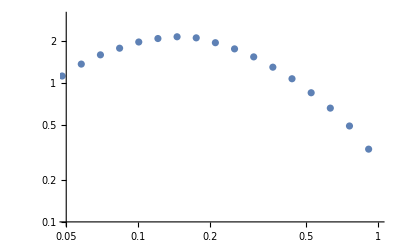

```mathematica
ListLogLogPlot[{f2tberr[1]},PlotRange->{{0.05,1},{1*10^-1,3}}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

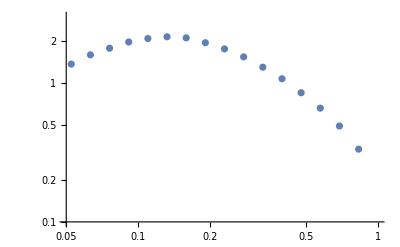

```mathematica
ListLogLogPlot[{f2tb[1]},PlotRange->{{0.05,1},{1*10^-1,3}}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

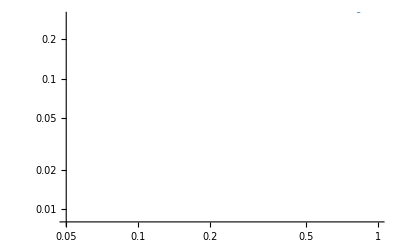

```mathematica
ListLogLogPlot[{f2tb[1],f2tb[2],f2tb[3],f2tb[4]},PlotRange->{{0.05,1},{8*10^-3,3*10^-1}}]
```

```mathematica
baseline=Import["./datafiles/baseline_pT2030.dat","Data","FieldSeparators"->","];
baselinetb[n_]:=Join[Table[{baseline[[i]][[1]]-(baseline[[i]][[2]])/2,baseline[[i]][[2n+1]]},{i,1,Length[baseline]}],{{baseline[[Length[baseline]]][[1]]+(baseline[[Length[baseline]]][[2]])/2,baseline[[Length[baseline]]][[2n+1]]}}]
baselinetberr[n_]:=Table[{baseline[[i]][[1]],baseline[[i]][[2n+1]]±baseline[[i]][[2n+2]]},{i,1,Length[baseline]}]
```

Import::nffil: File ./datafiles/baseline_pT2030.dat not found during Import.

```mathematica
ListPlot[{baselinetb[1],baselinetb[2],baselinetb[3]},Joined->True]
```

Part::partd: Part specification Symbol⟦1⟧ is longer than depth of object.

Part::partd: Part specification Symbol⟦2⟧ is longer than depth of object.

Part::partd: Part specification Symbol⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
pTeta00=Import["./datafiles/raw_eec_0_0.dat","Data","FieldSeparators"->","];
pTeta01=Import["./datafiles/raw_eec_0_1.dat","Data","FieldSeparators"->","];
pTeta02=Import["./datafiles/raw_eec_0_2.dat","Data","FieldSeparators"->","];

pTeta10=Import["./datafiles/raw_eec_1_0.dat","Data","FieldSeparators"->","];
pTeta11=Import["./datafiles/raw_eec_1_1.dat","Data","FieldSeparators"->","];
pTeta12=Import["./datafiles/raw_eec_1_2.dat","Data","FieldSeparators"->","];

pTeta20=Import["./datafiles/raw_eec_2_0.dat","Data","FieldSeparators"->","];
pTeta21=Import["./datafiles/raw_eec_2_1.dat","Data","FieldSeparators"->","];
pTeta22=Import["./datafiles/raw_eec_2_2.dat","Data","FieldSeparators"->","];
```

```mathematica
pTeta00tb[n_]:=Join[Table[{pTeta00[[i]][[1]]-(pTeta00[[i]][[2]])/2,(pTeta00[[i]][[2n+1]])/(pTeta00[[i]][[2]])},{i,1,Length[pTeta00]}],{{pTeta00[[Length[pTeta00]]][[1]]+(pTeta00[[Length[pTeta00]]][[2]])/2,(pTeta00[[Length[pTeta00]]][[2n+1]])/(pTeta00[[Length[pTeta00]]][[2]])}}]
pTeta00tberr[n_]:=Table[{pTeta00[[i]][[1]],(pTeta00[[i]][[2n+1]])/(pTeta00[[i]][[2]])±(pTeta00[[i]][[2n+2]])/(pTeta00[[i]][[2]])},{i,1,Length[pTeta00]}]

pTeta01tb[n_]:=Join[Table[{pTeta01[[i]][[1]]-(pTeta01[[i]][[2]])/2,(pTeta01[[i]][[2n+1]])/(pTeta01[[i]][[2]])},{i,1,Length[pTeta01]}],{{pTeta01[[Length[pTeta01]]][[1]]+(pTeta01[[Length[pTeta01]]][[2]])/2,(pTeta01[[Length[pTeta01]]][[2n+1]])/(pTeta01[[Length[pTeta01]]][[2]])}}]
pTeta01tberr[n_]:=Table[{pTeta01[[i]][[1]],(pTeta01[[i]][[2n+1]])/(pTeta01[[i]][[2]])±(pTeta01[[i]][[2n+2]])/(pTeta01[[i]][[2]])},{i,1,Length[pTeta01]}]

pTeta02tb[n_]:=Join[Table[{pTeta02[[i]][[1]]-(pTeta02[[i]][[2]])/2,(pTeta02[[i]][[2n+1]])/(pTeta02[[i]][[2]])},{i,1,Length[pTeta02]}],{{pTeta02[[Length[pTeta02]]][[1]]+(pTeta02[[Length[pTeta02]]][[2]])/2,(pTeta02[[Length[pTeta02]]][[2n+1]])/(pTeta02[[Length[pTeta02]]][[2]])}}]
pTeta02tberr[n_]:=Table[{pTeta02[[i]][[1]],(pTeta02[[i]][[2n+1]])/(pTeta02[[i]][[2]])±(pTeta02[[i]][[2n+2]])/(pTeta02[[i]][[2]])},{i,1,Length[pTeta02]}]

pTeta10tb[n_]:=Join[Table[{pTeta10[[i]][[1]]-(pTeta10[[i]][[2]])/2,(pTeta10[[i]][[2n+1]])/(pTeta10[[i]][[2]])},{i,1,Length[pTeta10]}],{{pTeta10[[Length[pTeta10]]][[1]]+(pTeta10[[Length[pTeta10]]][[2]])/2,(pTeta10[[Length[pTeta10]]][[2n+1]])/(pTeta10[[Length[pTeta10]]][[2]])}}]
pTeta10tberr[n_]:=Table[{pTeta10[[i]][[1]],(pTeta10[[i]][[2n+1]])/(pTeta10[[i]][[2]])±(pTeta10[[i]][[2n+2]])/(pTeta10[[i]][[2]])},{i,1,Length[pTeta10]}]

pTeta11tb[n_]:=Join[Table[{pTeta11[[i]][[1]]-(pTeta11[[i]][[2]])/2,(pTeta11[[i]][[2n+1]])/(pTeta11[[i]][[2]])},{i,1,Length[pTeta11]}],{{pTeta11[[Length[pTeta11]]][[1]]+(pTeta11[[Length[pTeta11]]][[2]])/2,(pTeta11[[Length[pTeta11]]][[2n+1]])/(pTeta11[[Length[pTeta11]]][[2]])}}]
pTeta11tberr[n_]:=Table[{pTeta11[[i]][[1]],(pTeta11[[i]][[2n+1]])/(pTeta11[[i]][[2]])±(pTeta11[[i]][[2n+2]])/(pTeta11[[i]][[2]])},{i,1,Length[pTeta11]}]

pTeta12tb[n_]:=Join[Table[{pTeta12[[i]][[1]]-(pTeta12[[i]][[2]])/2,(pTeta12[[i]][[2n+1]])/(pTeta12[[i]][[2]])},{i,1,Length[pTeta12]}],{{pTeta12[[Length[pTeta12]]][[1]]+(pTeta12[[Length[pTeta12]]][[2]])/2,(pTeta12[[Length[pTeta12]]][[2n+1]])/(pTeta12[[Length[pTeta12]]][[2]])}}]
pTeta12tberr[n_]:=Table[{pTeta12[[i]][[1]],(pTeta12[[i]][[2n+1]])/(pTeta12[[i]][[2]])±(pTeta12[[i]][[2n+2]])/(pTeta12[[i]][[2]])},{i,1,Length[pTeta12]}]

pTeta20tb[n_]:=Join[Table[{pTeta20[[i]][[1]]-(pTeta20[[i]][[2]])/2,(pTeta20[[i]][[2n+1]])/(pTeta20[[i]][[2]])},{i,1,Length[pTeta20]}],{{pTeta20[[Length[pTeta20]]][[1]]+(pTeta20[[Length[pTeta20]]][[2]])/2,(pTeta20[[Length[pTeta20]]][[2n+1]])/(pTeta20[[Length[pTeta20]]][[2]])}}]
pTeta20tberr[n_]:=Table[{pTeta20[[i]][[1]],(pTeta20[[i]][[2n+1]])/(pTeta20[[i]][[2]])±(pTeta20[[i]][[2n+2]])/(pTeta20[[i]][[2]])},{i,1,Length[pTeta20]}]

pTeta21tb[n_]:=Join[Table[{pTeta21[[i]][[1]]-(pTeta21[[i]][[2]])/2,(pTeta21[[i]][[2n+1]])/(pTeta21[[i]][[2]])},{i,1,Length[pTeta21]}],{{pTeta21[[Length[pTeta21]]][[1]]+(pTeta21[[Length[pTeta21]]][[2]])/2,(pTeta21[[Length[pTeta21]]][[2n+1]])/(pTeta21[[Length[pTeta21]]][[2]])}}]
pTeta21tberr[n_]:=Table[{pTeta21[[i]][[1]],(pTeta21[[i]][[2n+1]])/(pTeta21[[i]][[2]])±(pTeta21[[i]][[2n+2]])/(pTeta21[[i]][[2]])},{i,1,Length[pTeta21]}]

pTeta22tb[n_]:=Join[Table[{pTeta22[[i]][[1]]-(pTeta22[[i]][[2]])/2,(pTeta22[[i]][[2n+1]])/(pTeta22[[i]][[2]])},{i,1,Length[pTeta22]}],{{pTeta22[[Length[pTeta22]]][[1]]+(pTeta22[[Length[pTeta22]]][[2]])/2,(pTeta22[[Length[pTeta22]]][[2n+1]])/(pTeta22[[Length[pTeta22]]][[2]])}}]
pTeta22tberr[n_]:=Table[{pTeta22[[i]][[1]],(pTeta22[[i]][[2n+1]])/(pTeta22[[i]][[2]])±(pTeta22[[i]][[2n+2]])/(pTeta22[[i]][[2]])},{i,1,Length[pTeta22]}]
```

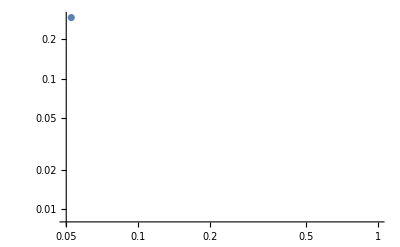

```mathematica
ListLogLogPlot[{pTeta00tb[1]},PlotRange->{{0.05,1},{8*10^-3,3*10^-1}}]
```

```mathematica
ListLogLogPlot[{pTeta00tb[1]},PlotRange->{{0.05,1},{8*10^-3,3*10^-1}}]
```

-Graphics-

```mathematica
pTetaheat=Import["./datafiles/pTetaheat.dat","Data","FieldSeparators"->","];
```

```mathematica
pTetatb[n_]:=Table[{pTetaheat[[i]][[1]]±(pTetaheat[[i]][[2]])/2,pTetaheat[[i]][[3]]±(pTetaheat[[i]][[4]])/2,pTetaheat[[i]][[2n+3]]±(pTetaheat[[i]][[2n+3]])/2},{i,1,Length[pTetaheat]}]
```

```mathematica
pTetatb[n_]:=Table[{pTetaheat[[i]][[1]],pTetaheat[[i]][[3]],pTetaheat[[i]][[2n+3]]},{i,1,Length[pTetaheat]}]
```

```mathematica
pTetatb2[n_]:=Table[{Log10[pTetaheat[[i]][[1]]],pTetaheat[[i]][[3]],pTetaheat[[i]][[2n+1]]},{i,1,Length[pTetaheat]}]
```

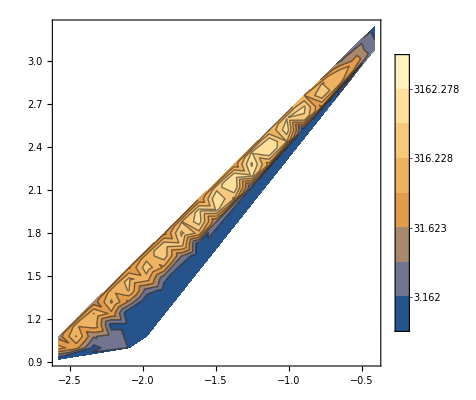

```mathematica
ListContourPlot[pTetatb[1],ScalingFunctions->{"Log10","Log10","Log10"},PlotLegends->Automatic]
```

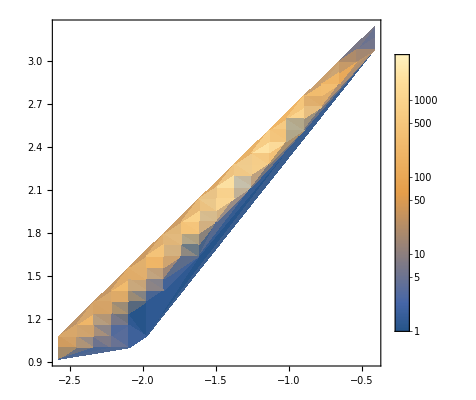

```mathematica
ListDensityPlot[pTetatb[1],ScalingFunctions->{"Log10","Log10","Log10"},PlotLegends->Automatic]
```

```mathematica
ListDensityPlot[pTetatb[1],ScalingFunctions->{"Log10","Log10","Log10"},PlotLegends->Automatic]
```

-Graphics-

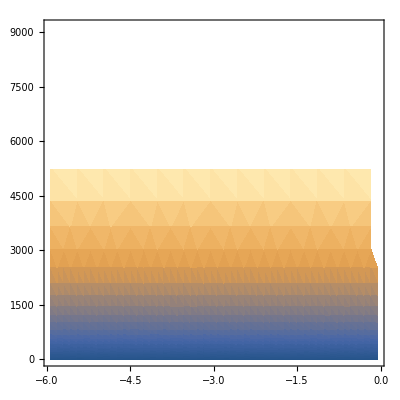

```mathematica
ListDensityPlot[pTetatb2[1]]
```

```mathematica
marker1=Graphics[{or,Disk[]}];
marker2=Graphics[{bl,Disk[]}];
marker3=Graphics[{gr,Disk[]}];
marker4=Graphics[{pur,Disk[]}];
```

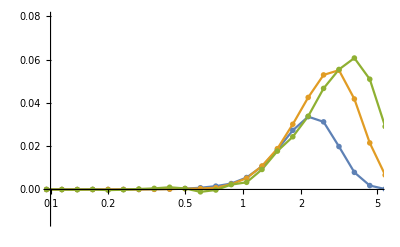

```mathematica
ListLogLinearPlot[{f3tb[1],f3tb[2],f3tb[3]},PlotRange->{{0.1,5},{-0.015,0.08}}, PlotMarkers->{marker1,0.021},Joined->True]
```

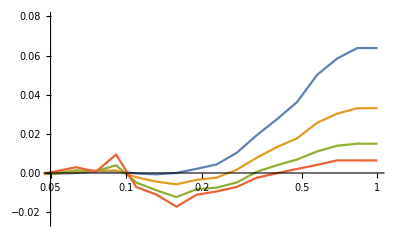

```mathematica
ListLogLinearPlot[{f4tb[1],f4tb[2],f4tb[3],f4tb[4]},PlotRange->{{0.05,1},{-0.025,0.08}},Joined->True]
```

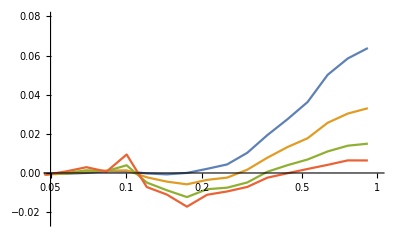

```mathematica
ListLogLinearPlot[{fig4[[;;,{1,3}]],fig4[[;;,{1,5}]],fig4[[;;,{1,7}]],fig4[[;;,{1,9}]]},PlotRange->{{0.05,1},{-0.025,0.08}},Joined->True]
```

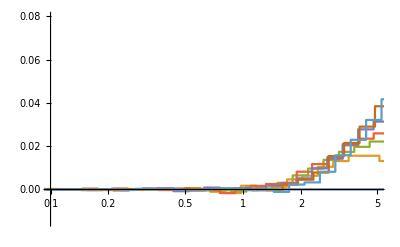

```mathematica
ListLogLinearPlot[{f5tb[1],f5tb[2],f5tb[3],f5tb[4],f5tb[5],f5tb[6],f5tb[7]},PlotRange->{{0.1,5},{-0.015,0.08}},Joined->True,InterpolationOrder->0]
```

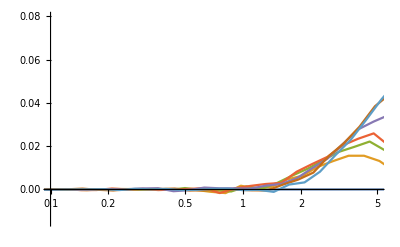

```mathematica
ListLogLinearPlot[{f5tb[1],f5tb[2],f5tb[3],f5tb[4],f5tb[5],f5tb[6],f5tb[7]},PlotRange->{{0.1,5},{-0.015,0.08}},Joined->True]
```

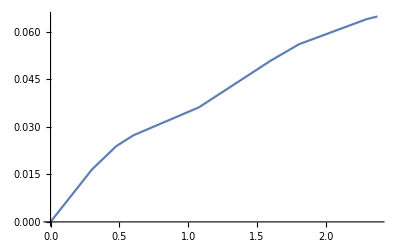

```mathematica
ListPlot[{fig5insert[[;;,{1,2}]]},Joined->True]
```

# Fig 2

```mathematica
dkgr
```

dkgr

```mathematica
sand
```

sand

```mathematica
{RGBColor[233/200,193/200,149/200],Thickness[thsize]}
```

{RGBColor[Rational[233, 200], Rational[193, 200], Rational[149, 200]],Thickness[0.004]}

```mathematica
dkgr={RGBColor[25/255,79/255,93/255],Thickness[thsize]};
ligr={RGBColor[46/255,158/255,144/255],Thickness[thsize]};
ligrr={RGBColor[145/255,177/255,145/255],Thickness[thsize]};
```

```mathematica
sand={RGBColor[233/255,193/255,149/255],Thickness[thsize]};
```

```mathematica
thsize=0.004;
lgy={RGBColor[0.2,0.2,0.2],Thickness[thsize]};
lgyfill=RGBColor[0.85,0.85,0.85];
dgy={RGBColor[0,0,0],Thickness[thsize]};
dgyfill=RGBColor[0.5,0.5,0.5];
gr={RGBColor[0,0.65,0],Thickness[thsize]};
grfill=RGBColor[0.35,1,0.35];
grth={RGBColor[0,0.65,0],Thickness[0.004]};
bl={RGBColor[0,0,1],Thickness[thsize]};
blfill=RGBColor[0.5,0.7,1];
blth={RGBColor[0,0,1],Thickness[0.004]};
or={RGBColor[2,0.1,0],Thickness[thsize]};
orfill=RGBColor[1,0.5,0];
orth={RGBColor[2,0.1,0],Thickness[0.004]};
skbl={RGBColor[109/250,175/250,237/250],Thickness[thsize]};
whfill=RGBColor[1,1,1];
white={RGBColor[1,1,1],Thickness[0.004]};
pur={RGBColor[0.5,0,0.5],Thickness[thsize]};
purfill=RGBColor[1,0.5,1];
mag={RGBColor[1,0,1],Thickness[thsize]};
blor1={RGBColor[0.33,0.033,0.66],Thickness[thsize]};
blor2={RGBColor[0.66,0.066,0.33],Thickness[thsize]};
re={RGBColor[224/250,31/250,31/250],Thickness[thsize]};
(*lior={RGBColor[240/250,167/250,65/250],Thickness[thsize]};
dkor={RGBColor[227/250,121/250,7/250],Thickness[thsize]};*)
```

```mathematica
or={RGBColor[2,0.1,0],Thickness[thsize]};
dkor={RGBColor[255/255,150/255,113/255],Thickness[thsize]};
lior={RGBColor[255/255,199/255,95/255],Thickness[thsize]};
```

```mathematica
marker1=Graphics[{skbl[[1]],Disk[]}];
marker2=Graphics[{lior[[1]],Disk[]}];
marker3=Graphics[{dkor[[1]],Disk[]}];
marker4=Graphics[{or[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{f2tb[1],f2tb[2],f2tb[3],f2tb[4]},PlotRange->{{0.05,1},{0.5*10^-1,3}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{skbl,lior,dkor,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{f2tberr[1],f2tberr[2],f2tberr[3],f2tberr[4]},PlotRange->{{0.05,1},{3*10^-1,5}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{skbl,lior,dkor,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.38],Log[0.03],skbl,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.023],lior,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0175],dkor,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0135],or,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[3.9]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[3.2]}] }]];
legend=ListPlot[{{{Log[0.405],Log[0.03]±0.1}},{{Log[0.405],Log[0.023]±0.1}},{{Log[0.405],Log[0.0175]±0.1}},{{Log[0.405],Log[0.0135]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{skbl[[1]],lior[[1]],dkor[[1]],or[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
{RGBColor[227/255,166/255,102/255],Thickness[thsize]}
```

{RGBColor[Rational[227, 255], Rational[166, 255], Rational[2, 5]],Thickness[0.004]}

```mathematica
dkgr={RGBColor[0,37/255,48/255],Thickness[thsize]};
ligr={RGBColor[0,112/255,88/255],Thickness[thsize]};
ligrr={RGBColor[1/255,173/255,158/255],Thickness[thsize]};
```

```mathematica
sand={RGBColor[227/255,166/255,102/255],Thickness[thsize]};
```

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{f2tb[1],f2tb[2],f2tb[3],f2tb[4]},PlotRange->{{0.05,1},{0.5*10^-1,3}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{f2tberr[1],f2tberr[2],f2tberr[3],f2tberr[4]},PlotRange->{{0.05,1},{3*10^-1,5}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.38],Log[0.03],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.023],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0175],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0135],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.22],Log[3.9]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.22],Log[3.2]}] }]];
legend=ListPlot[{{{Log[0.405],Log[0.03]±0.1}},{{Log[0.405],Log[0.023]±0.1}},{{Log[0.405],Log[0.0175]±0.1}},{{Log[0.405],Log[0.0135]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

# Fig 3

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{gr[[1]],Disk[]}];
marker3=Graphics[{or[[1]],Disk[]}];
marker4=Graphics[{pur[[1]],Disk[]}];
predictionplot=ListLogLinearPlot[{f3tb[1],f3tb[2],f3tb[3]},PlotRange->{{0.1,6},{-0.015,0.08}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,gr,or,pur}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.3],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLinearPlot[{f3tberr[1],f3tberr[2],f3tberr[3]},PlotRange->{{0.2,5.3},{-0.015,0.065}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{bl,gr,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.3],0.03,bl,orfill,""MaTeX["p_T \\in 5\\text{-}10\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],0.0225,gr,blfill,""MaTeX["p_T \\in 10\\text{-}20\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],0.015,or,blfill,""MaTeX["p_T \\in 20\\text{-}30\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+{}^{197}\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.45],0.053}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[0.32],0.03±0.002}},{{Log[0.32],0.0225±0.002}},{{Log[0.32],0.015±0.002}},{{Log[Sqrt[5]],-0.01}},{{Log[Sqrt[10]],-0.01}},{{Log[Sqrt[20]],-0.01}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026}},IntervalMarkersStyle->{bl[[1]],gr[[1]],or[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{gr[[1]],Disk[]}];
marker3=Graphics[{or[[1]],Disk[]}];
marker4=Graphics[{pur[[1]],Disk[]}];
predictionplot=ListLogLinearPlot[{f3ReAtb[1],f3ReAtb[2],f3ReAtb[3]},PlotRange->{{0.1,6},{-0.4,2.5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,gr,or,pur}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.3],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLinearPlot[{f3ReAtberr[1],f3ReAtberr[2],f3ReAtberr[3]},PlotRange->{{0.2,5.3},{-0.4,2.5}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{bl,gr,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.3],1.2,bl,orfill,""MaTeX["p_T \\in 5\\text{-}10\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],0.95,gr,blfill,""MaTeX["p_T \\in 10\\text{-}20\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],0.7,or,blfill,""MaTeX["p_T \\in 20\\text{-}30\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+{}^{197}\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{-0.6,1.75}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[0.32],1.2±0.075}},{{Log[0.32],0.95±0.075}},{{Log[0.32],0.7±0.075}},{{Log[Sqrt[5]],-0.01}},{{Log[Sqrt[10]],-0.01}},{{Log[Sqrt[20]],-0.01}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026}},IntervalMarkersStyle->{bl[[1]],gr[[1]],or[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

3332 lines of corrupt data deleted.

{1,2.,3.,4.,12.,40.,64.,197.002,238.002}

```mathematica
or={RGBColor[2,0.1,0],Thickness[thsize]};
re={RGBColor[250/250,1/250,1/250],Thickness[thsize]};
(*lior={RGBColor[240/250,167/250,65/250],Thickness[thsize]};
dkor={RGBColor[227/250,121/250,7/250],Thickness[thsize]};*)
dkor={RGBColor[255/255,150/255,113/255],Thickness[thsize]};
lior={RGBColor[255/255,199/255,95/255],Thickness[thsize]};
ye={RGBColor[227/250,200/250,7/250],Thickness[thsize]};
```

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{skbl[[1]],Disk[]}];
marker3=Graphics[{pur[[1]],Disk[]}];
marker4=Graphics[{gr[[1]],Disk[]}];
marker5=Graphics[{lior[[1]],Disk[]}];
marker6=Graphics[{dkor[[1]],Disk[]}];
marker7=Graphics[{re[[1]],Disk[]}];
predictionplot=ListPlot[{f5tb[3],f5tb[4],f5tb[5],f5tb[6],f5tb[7],f5tb[8],f5tb[9]},PlotRange->{{0.1,5},{-0.015,0.08}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.07],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];

predictionplot2=ListPlot[{f5tberr[3],f5tberr[4],f5tberr[5],f5tberr[6],f5tberr[7],f5tberr[8],f5tberr[9]},PlotRange->{{0.1,238^(1/6)*5},{-0.015,0.08}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021},{marker5,0.021},{marker6,0.021},{marker7,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[1.9],0.07,bl,orfill,""MaTeX["e+{}^3\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.063,skbl,blfill,""MaTeX["e+{}^4\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.056,pur,grfill,""MaTeX["e+{}^{12}\\text{C}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.049,gr,purfill,""MaTeX["e+{}^{40}\\text{Ca}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.042,lior,blfill,""MaTeX["e+{}^{64}\\text{Cu}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.035,dkor,blfill,""MaTeX["e+{}^{197}\\text{Au}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.028,re,blfill,""MaTeX["e+{}^{238}\\text{U}"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.11],0.53}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[2.03],0.07±0.002}},{{Log[2.03],0.063±0.002}},{{Log[2.03],0.056±0.002}},{{Log[2.03],0.049±0.002}},{{Log[2.03],0.042±0.002}},{{Log[2.03],0.035±0.002}},{{Log[2.03],0.028±0.002}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026},{marker5,0.026},{marker6,0.026},{marker7,0.026}},IntervalMarkersStyle->{bl[[1]],skbl[[1]],pur[[1]],gr[[1]],lior[[1]],dkor[[1]],re[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{skbl[[1]],Disk[]}];
marker3=Graphics[{pur[[1]],Disk[]}];
marker4=Graphics[{gr[[1]],Disk[]}];
marker5=Graphics[{lior[[1]],Disk[]}];
marker6=Graphics[{dkor[[1]],Disk[]}];
marker7=Graphics[{re[[1]],Disk[]}];
predictionplot=ListLogLinearPlot[{f5tb[3],f5tb[4],f5tb[5],f5tb[6],f5tb[7],f5tb[8],f5tb[9]},PlotRange->{{0.1,5},{-0.015,0.08}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.07],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];

predictionplot2=ListLogLinearPlot[{f5tberr[3],f5tberr[4],f5tberr[5],f5tberr[6],f5tberr[7],f5tberr[8],f5tberr[9]},PlotRange->{{0.1,238^(1/6)*5},{-0.015,0.08}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021},{marker5,0.021},{marker6,0.021},{marker7,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[1.9],0.07,bl,orfill,""MaTeX["e+{}^3\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.063,skbl,blfill,""MaTeX["e+{}^4\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.056,pur,grfill,""MaTeX["e+{}^{12}\\text{C}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.049,gr,purfill,""MaTeX["e+{}^{40}\\text{Ca}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.042,lior,blfill,""MaTeX["e+{}^{64}\\text{Cu}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.035,dkor,blfill,""MaTeX["e+{}^{197}\\text{Au}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.028,re,blfill,""MaTeX["e+{}^{238}\\text{U}"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.11],0.53}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[2.03],0.07±0.002}},{{Log[2.03],0.063±0.002}},{{Log[2.03],0.056±0.002}},{{Log[2.03],0.049±0.002}},{{Log[2.03],0.042±0.002}},{{Log[2.03],0.035±0.002}},{{Log[2.03],0.028±0.002}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026},{marker5,0.026},{marker6,0.026},{marker7,0.026}},IntervalMarkersStyle->{bl[[1]],skbl[[1]],pur[[1]],gr[[1]],lior[[1]],dkor[[1]],re[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{skbl[[1]],Disk[]}];
marker3=Graphics[{pur[[1]],Disk[]}];
marker4=Graphics[{gr[[1]],Disk[]}];
marker5=Graphics[{lior[[1]],Disk[]}];
marker6=Graphics[{dkor[[1]],Disk[]}];
marker7=Graphics[{re[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{f5ReAtb[3],f5ReAtb[4],f5ReAtb[5],f5ReAtb[6],f5ReAtb[7],f5ReAtb[8],f5ReAtb[9]},PlotRange->{{0.1,5},{0.1,3.3}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.07],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];

predictionplot2=ListLogLogPlot[{f5ReAtberr[3],f5ReAtberr[4],f5ReAtberr[5],f5ReAtberr[6],f5ReAtberr[7],f5ReAtberr[8],f5ReAtberr[9]},PlotRange->{{0.1,238^(1/6)*5},{-0.75,3.3}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021},{marker5,0.021},{marker6,0.021},{marker7,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[2.12],2.8,bl,orfill,""MaTeX["e+{}^3\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],2.5,skbl,blfill,""MaTeX["e+{}^4\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],2.2,pur,grfill,""MaTeX["e+{}^{12}\\text{C}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],1.9,gr,purfill,""MaTeX["e+{}^{40}\\text{Ca}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],1.6,lior,blfill,""MaTeX["e+{}^{64}\\text{Cu}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],1.3,dkor,blfill,""MaTeX["e+{}^{197}\\text{Au}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],1.0,re,blfill,""MaTeX["e+{}^{238}\\text{U}"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],4}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{0.1,4}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,4},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,4},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,4},{-1,0}] }]];
legend=ListPlot[{{{Log[2.25],2.8±0.1}},{{Log[2.25],2.5±0.1}},{{Log[2.25],2.2±0.1}},{{Log[2.25],1.9±0.1}},{{Log[2.25],1.6±0.1}},{{Log[2.25],1.3±0.1}},{{Log[2.25],1.0±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026},{marker5,0.026},{marker6,0.026},{marker7,0.026}},IntervalMarkersStyle->{bl[[1]],skbl[[1]],pur[[1]],gr[[1]],lior[[1]],dkor[[1]],re[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
f5tb2[n_]:=Join[Table[{(fig5[[i]][[1]]-(fig5[[i]][[2]])/2),fig5[[i]][[2n+1]]},{i,1,Length[fig5]}],{{(fig5[[Length[fig5]]][[1]]+(fig5[[Length[fig5]]][[2]])/2),fig5[[Length[fig5]]][[2n+1]]}}]
f5tberr2[n_]:=Table[{fig5[[i]][[1]],fig5[[i]][[2n+1]]±fig5[[i]][[2n+2]]},{i,1,Length[fig5]}]
```

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{skbl[[1]],Disk[]}];
marker3=Graphics[{pur[[1]],Disk[]}];
marker4=Graphics[{gr[[1]],Disk[]}];
marker5=Graphics[{lior[[1]],Disk[]}];
marker6=Graphics[{dkor[[1]],Disk[]}];
marker7=Graphics[{re[[1]],Disk[]}];
predictionplot=ListLogLinearPlot[{f5tb2[3],f5tb2[4],f5tb2[5],f5tb2[6],f5tb2[7],f5tb2[8],f5tb2[9]},PlotRange->{{0.1,5},{-0.015,0.08}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.07],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];

predictionplot2=ListLogLinearPlot[{f5tberr2[3],f5tberr2[4],f5tberr2[5],f5tberr2[6],f5tberr2[7],f5tberr2[8],f5tberr2[9]},PlotRange->{{0.1,5},{-0.015,0.08}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021},{marker5,0.021},{marker6,0.021},{marker7,0.021}},Frame->True, FrameStyle->Directive[Black,20],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.5*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.5*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.15],0.07,bl,orfill,""MaTeX["e+{}^3\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.063,skbl,blfill,""MaTeX["e+{}^4\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.056,pur,grfill,""MaTeX["e+{}^{12}\\text{C}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.049,gr,purfill,""MaTeX["e+{}^{40}\\text{Ca}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.042,lior,blfill,""MaTeX["e+{}^{64}\\text{Cu}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.035,dkor,blfill,""MaTeX["e+{}^{197}\\text{Au}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.028,re,blfill,""MaTeX["e+{}^{238}\\text{U}"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.11],0.53}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[0.16],0.07±0.002}},{{Log[0.16],0.063±0.002}},{{Log[0.16],0.056±0.002}},{{Log[0.16],0.049±0.002}},{{Log[0.16],0.042±0.002}},{{Log[0.16],0.035±0.002}},{{Log[0.16],0.028±0.002}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026},{marker5,0.026},{marker6,0.026},{marker7,0.026}},IntervalMarkersStyle->{bl[[1]],skbl[[1]],pur[[1]],gr[[1]],lior[[1]],dkor[[1]],re[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
LinearModelFit[fig5insert,x,x]
```

FittedModel[0.00713348+0.0230583 x]

```mathematica
Log[y]=number Log[A]
```

Set::write: Tag Log in Log[y] is Protected.

number Log[A]

```mathematica
Exit[]
```

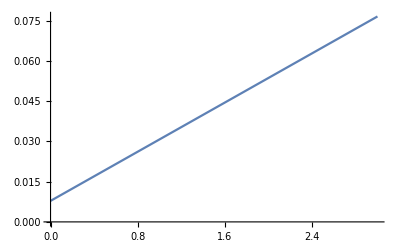

```mathematica
Plot[0.022907x+0.007828,{x,0,3}]
```

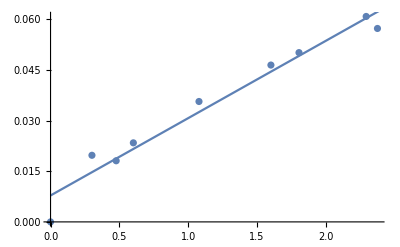

```mathematica
Show[ListPlot[fig5insert],Plot[0.022907x+0.007828,{x,0,3}]]
```

```mathematica
fig5insert
```

```mathematica
Table[{{fig5insert[[i]][[1]],Log10[fig5insert[[i]][[2]]]}},{i,2,Length[fig5insert]}]//StandardForm
```

{{{0.30103,-1.78216}},{{0.477121,-1.62236}},{{0.60206,-1.56406}},{{1.07918,-1.44219}},{{1.60206,-1.29358}},{{1.80618,-1.25181}},{{2.29447,-1.19479}},{{2.37658,-1.18871}}}

```mathematica
Table[{{fig5insert[[i]][[1]],fig5insert[[i]][[2]]}},{i,3,Length[fig5insert]}]//StandardForm
```

{{{0.477121,0.0181179}},{{0.60206,0.0234332}},{{1.07918,0.0343877}},{{1.60206,0.0399072}},{{1.80618,0.0507151}},{{2.29447,0.059843}},{{2.37658,0.06106}}}

```mathematica
Table[{{fig5insert[[i]][[1]],Log10[fig5insert[[i]][[2]]]}},{i,3,Length[fig5insert]}]//StandardForm
```

{{{0.477121,-1.74189}},{{0.60206,-1.63017}},{{1.07918,-1.4636}},{{1.60206,-1.39895}},{{1.80618,-1.29486}},{{2.29447,-1.22299}},{{2.37658,-1.21424}}}

```mathematica
fig5insertlist={{{0.30103,-1.7821608692210524}},{{0.477121,-1.622355043905958}},{{0.60206,-1.5640617168455602}},{{1.07918,-1.4421933464363175}},{{1.60206,-1.2935792435337619}},{{1.80618,-1.2518142995776131}},{{2.29447,-1.1947942088868977}},{{2.37658,-1.18870858448702}}};
```

```mathematica
fig5insertlist={{{0.30103,-1.704615452029604}},{{0.477121,-1.7418921417179711}},{{0.60206,-1.6301684007992265}},{{1.07918,-1.463596870723851}},{{1.60206,-1.3989487424542169}},{{1.80618,-1.2948627138361388}},{{2.29447,-1.222986642904497}},{{2.37658,-1.2142432000373569}}}
```

{{{0.30103,-1.70462}},{{0.477121,-1.74189}},{{0.60206,-1.63017}},{{1.07918,-1.4636}},{{1.60206,-1.39895}},{{1.80618,-1.29486}},{{2.29447,-1.22299}},{{2.37658,-1.21424}}}

```mathematica
Log10[3]//N
```

0.477121

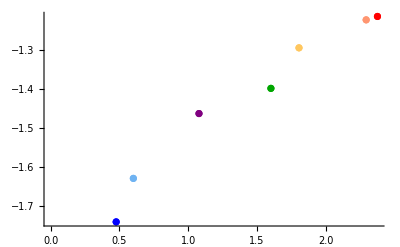

```mathematica
ListPlot[fig5insertlist,PlotStyle->{White,bl,skbl,pur,gr,lior,dkor,re}]
```

```mathematica
LinearModelFit[Table[{fig5insert[[i]][[1]],Log10[fig5insert[[i]][[2]]]},{i,2,Length[fig5insert]}],x,x]
```

FittedModel[-1.76182+0.261411 x]

```mathematica
10^-1.79442
```

0.0160539

```mathematica
0.0161
```

```mathematica
Log10[peak]=-1.79442+0.254687 Log10[A]
```

```mathematica
Log[4]//N
```

1.38629

```mathematica
Alist
```

{1,2.,3.,4.,12.,40.,64.,197.002,238.002}

```mathematica
10^-1.76182
```

0.0173053

```mathematica
fig
```

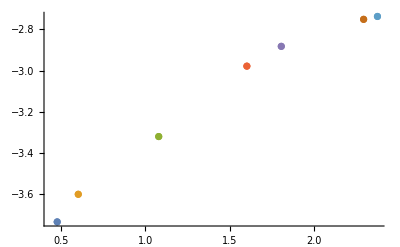

```mathematica
ListPlot[Table[{{fig5insert[[i]][[1]],Log[fig5insert[[i]][[2]]]}},{i,3,Length[fig5insert]}]]
```

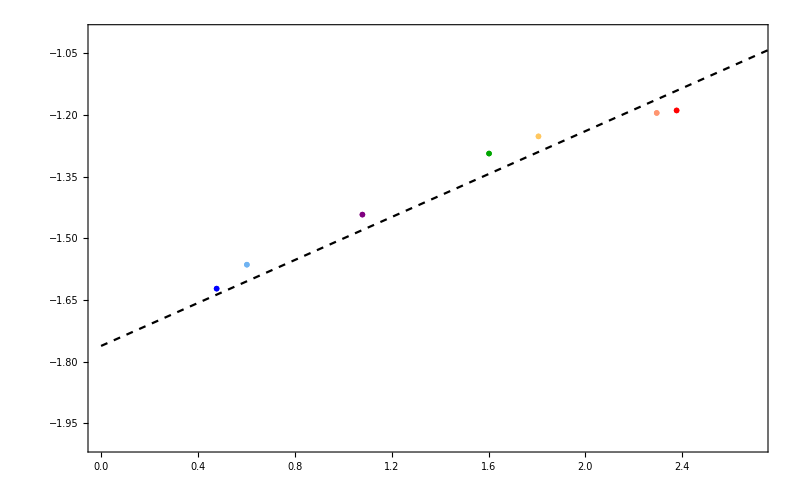

```mathematica
predictionplot2=ListPlot[fig5insertlist,PlotRange->{{0,2.7},{-1.0,-2}}, PlotMarkers->{{marker0,0.05},{marker1,0.05},{marker2,0.05},{marker3,0.05},{marker4,0.05},{marker5,0.05},{marker6,0.05},{marker7,0.05}},Joined->True,Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\log(\\text{Peak Value})",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\log A"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{White,bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.11],0.53}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot=ListPlot[Table[{fig5insert[[i]][[1]],Log10[fig5insert[[i]][[2]]]},{i,3,Length[fig5insert]}],Joined->True,PlotStyle->{Dashed,Black}];
predictionplot=Plot[-1.7618246920348026+0.26141129268304425 x,{x,0,3},PlotStyle->{Dashed,Black}];
Show[predictionplot2,predictionplot]
```

# Supplemental

## pT-eta dependence

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{f2tb[1],f2tb[2],f2tb[3],f2tb[4]},PlotRange->{{0.05,1},{0.5*10^-1,3}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{f2tberr[1],f2tberr[2],f2tberr[3],f2tberr[4]},PlotRange->{{0.05,1},{3*10^-1,5}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.38],Log[0.03],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.023],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0175],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0135],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.22],Log[3.9]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.22],Log[3.2]}] }]];
legend=ListPlot[{{{Log[0.405],Log[0.03]±0.1}},{{Log[0.405],Log[0.023]±0.1}},{{Log[0.405],Log[0.0175]±0.1}},{{Log[0.405],Log[0.0135]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta00tb[1],pTeta00tb[2],pTeta00tb[3],pTeta00tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta00tberr[1],pTeta00tberr[2],pTeta00tberr[3],pTeta00tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta10tb[1],pTeta10tb[2],pTeta10tb[3],pTeta10tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta10tberr[1],pTeta10tberr[2],pTeta10tberr[3],pTeta10tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta11tb[1],pTeta11tb[2],pTeta11tb[3],pTeta11tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta11tberr[1],pTeta11tberr[2],pTeta11tberr[3],pTeta11tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta12tb[1],pTeta12tb[2],pTeta12tb[3],pTeta12tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta12tberr[1],pTeta12tberr[2],pTeta12tberr[3],pTeta12tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta20tb[1],pTeta20tb[2],pTeta20tb[3],pTeta20tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta20tberr[1],pTeta20tberr[2],pTeta20tberr[3],pTeta20tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta21tb[1],pTeta21tb[2],pTeta21tb[3],pTeta21tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta21tberr[1],pTeta21tberr[2],pTeta21tberr[3],pTeta21tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta22tb[1],pTeta22tb[2],pTeta22tb[3],pTeta22tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta22tberr[1],pTeta22tberr[2],pTeta22tberr[3],pTeta22tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

## K=0 comparison

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{gr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{baselinetb[1],baselinetb[2],baselinetb[3]},PlotRange->{{0.05,0.999},{1*10^-3,3*10^-1}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,gr,ligr,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],sand,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],gr,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],ligr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{baselinetberr[1],baselinetberr[2],baselinetberr[3]},PlotRange->{{0.05,1},{4*10^-3,1.5*10^-1}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,gr,ligr,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.38],Log[0.028],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.019],gr,blfill,""MaTeX["e+{}^{2}\\text{D, }K=0"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.013],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=0"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026}},IntervalMarkersStyle->{sand[[1]],gr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

## qhat

```mathematica
ListPlot3D[qhatxQdata,ScalingFunctions->{"Log10","Log10","Log10"}]
```

-Graphics3D-

```mathematica
Table[i,{i,0,0.42,0.42/6}]
```

{0.,0.07,0.14,0.21,0.28,0.35,0.42}

```mathematica
qhatxQK2=Import["./datafiles/qhat_data_Au_K2.dat","Data","FieldSeparators"->","];
qhatxQK4=Import["./datafiles/qhat_data_Au_K4.dat","Data","FieldSeparators"->","];
qhatxQK10=Import["./datafiles/qhat_data_Au_K10.dat","Data","FieldSeparators"->","];
xQcoord=Table[{10^i,10^j},{j,-3,0,(0-(-3))/20},{i,0,3,(3-0)/20}];
qhatxQdata=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQ[[i]][[j]]=="nan",0,qhatxQ[[i]][[j]]]},{i,5,Length[qhatxQ]},{j,1,Length[qhatxQ[[5]]]}],1],Abs[#[[3]]]>0&];
qhatxQdataK2=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQK2[[i]][[j]]=="nan",0,qhatxQK2[[i]][[j]]]},{i,5,Length[qhatxQK2]},{j,1,Length[qhatxQK2[[5]]]}],1],Abs[#[[3]]]>0&];
qhatxQdataK4=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQK4[[i]][[j]]=="nan",0,qhatxQK4[[i]][[j]]]},{i,5,Length[qhatxQK4]},{j,1,Length[qhatxQK4[[5]]]}],1],Abs[#[[3]]]>0&];
qhatxQdataK10=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQK10[[i]][[j]]=="nan",0,qhatxQK10[[i]][[j]]]},{i,5,Length[qhatxQK10]},{j,1,Length[qhatxQK10[[5]]]}],1],Abs[#[[3]]]>0&];
```

```mathematica
xQcoord=Table[{10^i,10^j},{j,-3,0,(0-(-3))/20},{i,0,3,(3-0)/20}];
qhatxQdata=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQ[[i]][[j]]=="nan",0,qhatxQ[[i]][[j]]]},{i,5,Length[qhatxQ]},{j,1,Length[qhatxQ[[5]]]}],1],Abs[#[[3]]]>0&];
```

```mathematica
ListContourPlot[qhatxQdataK2, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{0,0.90}},44,LegendMarkerSize->{20,605}],ColorFunction->(ColorData["BlueGreenYellow",Rescale[#,{0,0.90}]]&),ColorFunctionScaling->False,(*PlotLegends->{0,0.06,0.12,0.18,0.24,0.30,0.36,0.42},*)
FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->{{0.001,1},{1,1000},{0,0.90}}, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]

ListContourPlot[qhatxQdataK4, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{0,0.90}},44,LegendMarkerSize->{20,605}],ColorFunction->(ColorData["BlueGreenYellow",Rescale[#,{0,0.90}]]&),ColorFunctionScaling->False,(*PlotLegends->{0,0.06,0.12,0.18,0.24,0.30,0.36,0.42},*)
FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->{{0.001,1},{1,1000},{0,0.90}}, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]

ListContourPlot[qhatxQdataK10, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{0,0.90}},44,LegendMarkerSize->{20,605}],ColorFunction->(ColorData["BlueGreenYellow",Rescale[#,{0,0.90}]]&),ColorFunctionScaling->False,(*PlotLegends->{0,0.06,0.12,0.18,0.24,0.30,0.36,0.42},*)
FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->{{0.001,1},{1,1000},{0,0.90}}, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListContourPlot[qhatxQdataK10, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{0,0.90}},44,LegendMarkerSize->{20,605}],ColorFunction->(ColorData["BlueGreenYellow",Rescale[#,{0,0.90}]]&),ColorFunctionScaling->False,(*PlotLegends->{0,0.06,0.12,0.18,0.24,0.30,0.36,0.42},*)
FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->{{0.001,1},{1,1000},{0,0.90}}, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
Max[Table[qhatxQdataK10[[i]][[3]],{i,1,Length[qhatxQdataK10]}]]
```

0.903

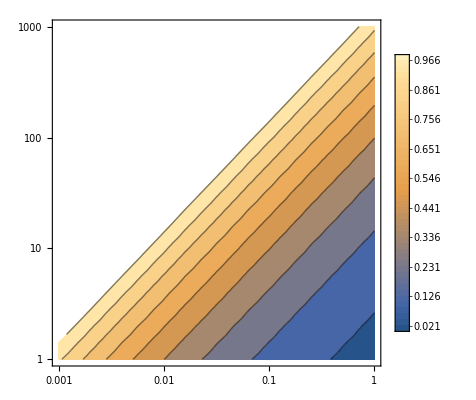

```mathematica
ListContourPlot[qhatxQdataK10, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{0,1}},46,LegendMarkerSize->{20,605}]]
```

```mathematica
PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData["SunsetColors",Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,
```

```mathematica
BarLegend[{"BlueGreenYellow",{0,0.90}},Ticks->Table[i,{i,0,0.90,0.90/6}],LegendMarkerSize->{20,605}]//StandardForm
```

```mathematica
ListContourPlot[qhatxQdata, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,0.48}},Ticks->Table[i,{i,0,0.48,0.48/6}],LegendMarkerSize->{20,605}],(*PlotLegends->{0,0.06,0.12,0.18,0.24,0.30,0.36,0.42},*)
FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[qhatxQdata, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},ColorFunction->"DeepSeaColors",
FrameLabel->{{Style[MaTeX["\\mathrm{Q^2[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
TicksStyle->Large,
```

```mathematica
ColorFunction->"SunsetColors","BlueGreenYellow",DeepSeaColors,
```

-Graphics-

## pT eta heat

```mathematica
pTetatb[n_]:=Table[{pTetaheat[[i]][[1]]+(pTetaheat[[i]][[2]])/2,pTetaheat[[i]][[3]]+(pTetaheat[[i]][[4]])/2,pTetaheat[[i]][[2n+3]]+0.1},{i,1,Length[pTetaheat]}]
```

```mathematica
BarLegend[{{"SunsetColors","Reverse"},{0,6}},Ticks->Table[i,{i,0,6,6/6}],LegendMarkerSize->{20,605}]
```

```mathematica
BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11]
```

```mathematica
Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{skbl,lior,dkor,or}, PlotRange->All,
```

```mathematica
ListDensityPlot[pTetatb[1]/. {x_,y_,z_}->{x,y,Log10[z]}, InterpolationOrder->0,Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[4]/. {x_,y_,z_}->{x,y,Log10[z]}, InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[5]/. {x_,y_,z_}->{x,y,Log10[z]},  InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[6]/. {x_,y_,z_}->{x,y,Log10[z]}, InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[7]/. {x_,y_,z_}->{x,y,Log10[z]},  InterpolationOrder->0,Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[8]/. {x_,y_,z_}->{x,y,Log10[z]}, InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[9]/. {x_,y_,z_}->{x,y,Log10[z]}, InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

# NP

```mathematica
f2tbtemp[n_]:=Table[{fig2[[i]][[1]]-(fig2[[i]][[2]])/2,(fig2[[i]][[2n+1]])/(fig2[[i]][[1]]-(fig2[[i]][[2]])/2)},{i,1,Length[fig2]}]
```

```mathematica
rr=1;
JqLONLL[2][20,θ^2/4,20];
```

```mathematica
NIntegrate[θ D[JqLONLL[2][20,z,20],z]/.{z->θ^2/4},{θ,0.5,1}]
```

NIntegrate::inumr: The integrand θ JqLONLL[2]^(0,1,0)[20,θ^2/4,20] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.5,1}}.

NIntegrate[θ ∂_z JqLONLL[2][20,z,20]/.{z→θ^2/4},{θ,0.5,1}]

```mathematica
LogLinearPlot[θ/0.206284 D[JqLONLL[2][20,z,20],z]/.{z->θ^2/4},{θ,0.01,1},PlotRange->{{0.05,1},{0,5}},PlotStyle->Red]
```

-Graphics-

```mathematica
1/20//N
```

0.05

```mathematica
NIntegrate[Interpolation[f2tbtemp[1]][x],{x,0.5,1}]
```

InterpolatingFunction::dmvali: The integration endpoint 1 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.0426119

```mathematica
NIntegrate[θ (D[JqLONLL[2][20,z,20],z]/.{z->θ^2/4})+4/(20 θ),{θ,0.5,1}]
```

NIntegrate::inumr: The integrand 1/(5 θ)+θ JqLONLL[2]^(0,1,0)[20,θ^2/4,20] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.5,1}}.

NIntegrate[θ (∂_z JqLONLL[2][20,z,20]/.{z→θ^2/4})+4/(20 θ),{θ,0.5,1}]

```mathematica
LogLinearPlot[1/0.344913(θ (D[JqLONLL[2][20,z,20],z]/.{z->θ^2/4})+4/(20 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0,5}},PlotStyle->{Green}]
```

-Graphics-

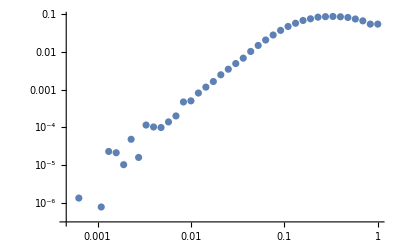

```mathematica
ListLogLogPlot[{pTeta22tb[1]}]
```

```mathematica
f2tbtemp[n_]:=Table[{fig2[[i]][[1]]-(fig2[[i]][[2]])/2,(fig2[[i]][[2n+1]])/(fig2[[i]][[1]]-(fig2[[i]][[2]])/2)},{i,1,Length[fig2]}]
```

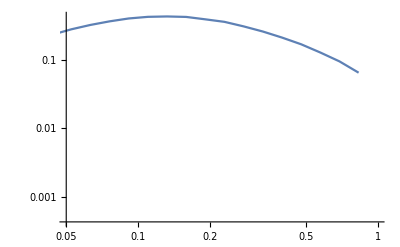

```mathematica
ListLogLogPlot[f2tbtemp[1],Joined->True,PlotRange->{{0.05,1},All}]
```

```mathematica
LogLogPlot[1/5 D[JqLONLL[2][20,z,20],z]/.{z->θ^2/4},{θ,0.01,1},PlotRange->{{0.05,1},{0.00001,10}},PlotStyle->Red]
```

-Graphics-

```mathematica
α[θ 20]/α[20]
```

α[20 θ]/α[20]

```mathematica
gTqq0[2]
```

gTqq0[2]

```mathematica
pTeta20tbtemp[n_]:=Table[{pTeta20[[i]][[1]]-(pTeta20[[i]][[2]])/2,(pTeta20[[i]][[2n+1]])/(pTeta20[[i]][[1]]-(pTeta20[[i]][[2]])/2)},{i,1,Length[pTeta20]}]
```

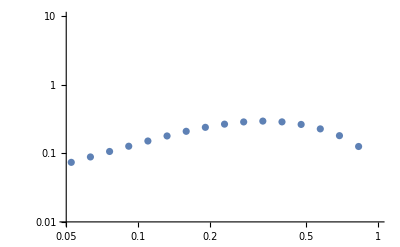

```mathematica
Show[ListLogLogPlot[pTeta20tbtemp[1],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/5},{}}],LogLogPlot[(1/4 θ( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[1/8 θ(1/5( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})+4/(5 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]]
```

```mathematica
pTeta20tbtemp[n_]:=Table[{pTeta20[[i]][[1]]-(pTeta20[[i]][[2]])/2,(pTeta20[[i]][[2n+1]])/(pTeta20[[i]][[1]]-(pTeta20[[i]][[2]])/2)},{i,1,Length[pTeta20]}]
pTeta21tbtemp[n_]:=Table[{pTeta21[[i]][[1]]-(pTeta21[[i]][[2]])/2,(pTeta21[[i]][[2n+1]])/(pTeta21[[i]][[1]]-(pTeta21[[i]][[2]])/2)},{i,1,Length[pTeta21]}]
pTeta22tbtemp[n_]:=Table[{pTeta22[[i]][[1]]-(pTeta22[[i]][[2]])/2,(pTeta22[[i]][[2n+1]])/(pTeta22[[i]][[1]]-(pTeta22[[i]][[2]])/2)},{i,1,Length[pTeta22]}]
```

```mathematica
LogLogPlot[(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red]
```

-Graphics-

```mathematica
Cosh[-Log[Tan[θ/2]]]
```

1/2 Cot[θ/2] (1+Tan[θ/2]^2)

```mathematica
LogLogPlot[1/4(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})+4/20 Cosh[-Log[Tan[θ/2]]]),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]
```

-Graphics-

```mathematica
Cosh[-Log[Tan[θ/2]]]
```

1/2 Cot[θ/2] (1+Tan[θ/2]^2)

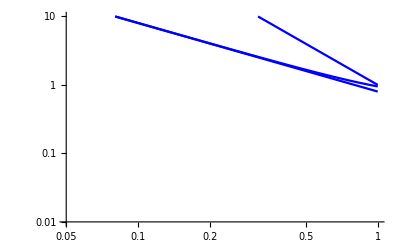

```mathematica
LogLogPlot[{4/5 Cosh[-Log[Tan[θ/2]]],4/(5 θ),1/θ^2},{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]
```

```mathematica
(D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})/.{θ->1}
```

JqLONLL[2]^(0,1,0)[5,1/4,5]+JqNLONLL[2]^(0,1,0)[5,1/4,5]

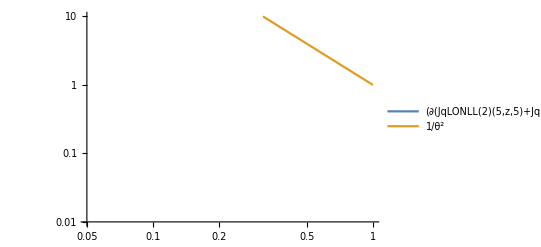

```mathematica
LogLogPlot[{(D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4}),1/θ^2},{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotLegends->"Expressions"]
```

```mathematica
Show[LogLogPlot[(1/4( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[(1/4( D[JqLONLL[2][10,z,10]+JqNLONLL[2][10,z,10],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue],LogLogPlot[(1/4( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Green]]
```

-Graphics-

```mathematica
Show[ListLogLogPlot[pTeta20tbtemp[1],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/5},{}}],LogLogPlot[(1/4( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[1/7((D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})+(2π 0.31)/(5 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]]
```

-Graphics-

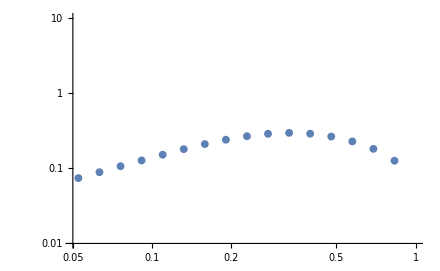

```mathematica
Show[ListLogLogPlot[pTeta20tbtemp[1],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/5},{}}],LogLogPlot[(1/4( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[1/8(1/5( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})+4/(5 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]]
```

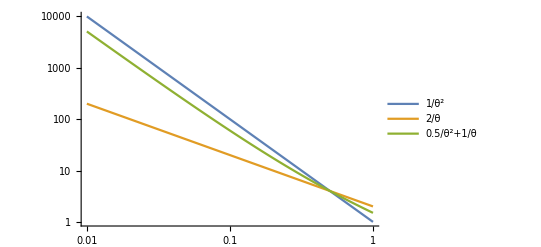

```mathematica
LogLogPlot[{1/θ^2,2/θ,0.5/θ^2+1/θ},{θ,0.01,1},PlotLegends->"Expressions"]
```

```mathematica
Log[Exp[x^-2]]
```

Log[ⅇ^(1/x^2)]

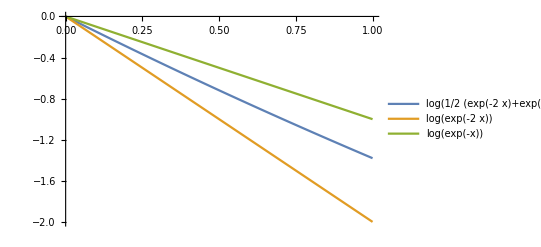

```mathematica
Plot[{Log[(Exp[-2x]+Exp[-x])/2],Log[Exp[-2x]],Log[Exp[-x]]},{x,0,1},PlotLegends->"Expressions"]
```

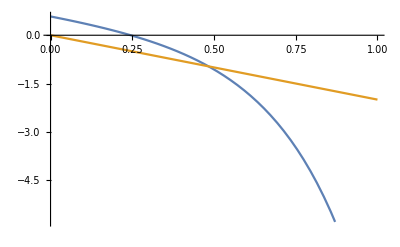

```mathematica
Plot[{-2x+Exp[x]-1/2 Exp[2x]+1/3 Exp[3x]-1/4 Exp[4x],-2x},{x,0,1}]
```

```mathematica
Log[]
```

Log::argt: Log called with 0 arguments; 1 or 2 arguments are expected.

Log[]

```mathematica
Series[Log[a/θ^2+b/θ],{θ,0,4}]
```

Log[a/θ^2]+(b θ)/a-(b^2 θ^2)/(2 a^2)+(b^3 θ^3)/(3 a^3)-(b^4 θ^4)/(4 a^4)+O[θ]^5

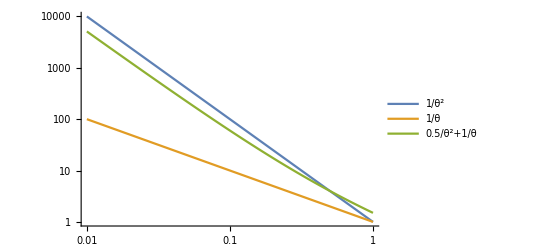

```mathematica
LogLogPlot[{1/θ^2,1/θ,0.5/θ^2+1/θ},{θ,0.01,1},PlotLegends->"Expressions"]
```

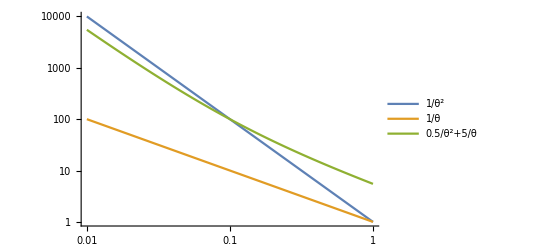

```mathematica
LogLogPlot[{1/θ^2,1/θ,0.5/θ^2+5/θ},{θ,0.01,1},PlotLegends->"Expressions"]
```

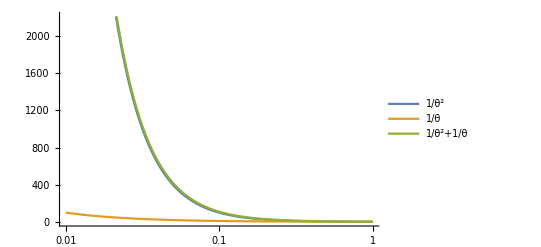

```mathematica
LogLinearPlot[{1/θ^2,1/θ,1/θ^2+1/θ},{θ,0.01,1},PlotLegends->"Expressions"]
```

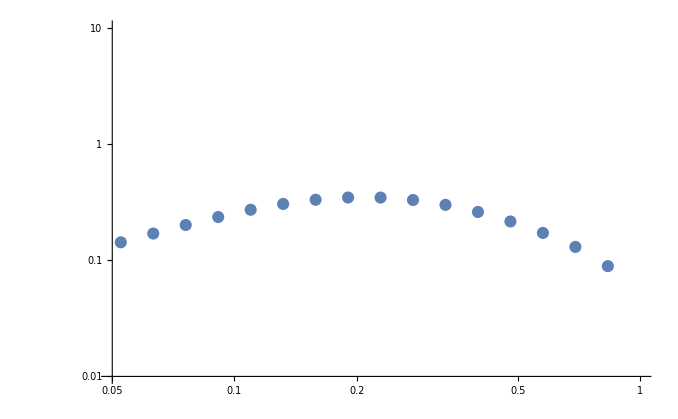

```mathematica
Show[ListLogLogPlot[pTeta21tbtemp[1],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/10},{}}],LogLogPlot[(1/5( D[JqLONLL[2][10,z,10]+JqNLONLL[2][10,z,10],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[1/6(1/5( D[JqLONLL[2][10,z,10]+JqNLONLL[2][10,z,10],z]/.{z->θ^2/4})+4/(10θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]]
```

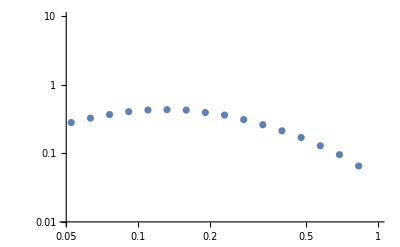

```mathematica
Show[ListLogLogPlot[pTeta22tbtemp[1],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/20},{}}],LogLogPlot[(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[1/4(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})+4/(20 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]]
```

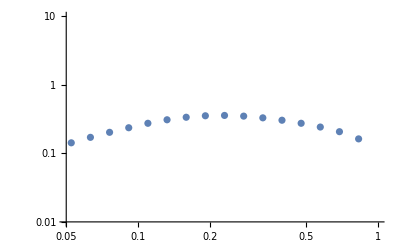

```mathematica
ListLogLogPlot[pTeta21tbtemp[2],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/10},{}}]
```

```mathematica
LogLogPlot[1/2(1/5( D[JqLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})+1/(20 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.00001,10}},PlotStyle->Blue]
```

-Graphics-

```mathematica
LogLogPlot[(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red]
```

-Graphics-

```mathematica
LogLogPlot[1/4(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})+4/(20 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]
```

-Graphics-

```mathematica
ListLogLogPlot[f2tbtemp[1],PlotRange->{{0.05,1},{0.01,10}}]
```

-Graphics-

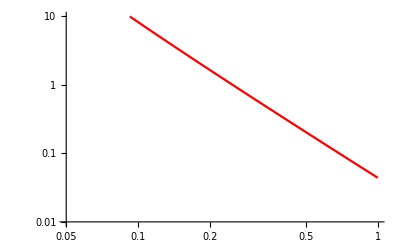
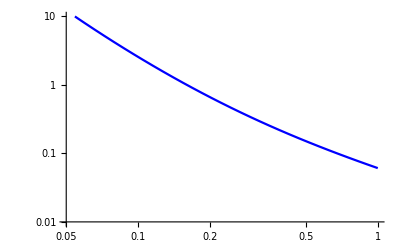
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

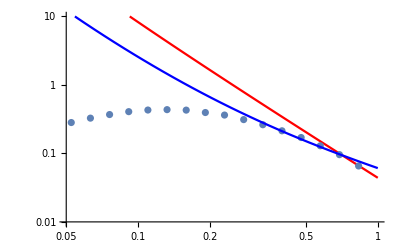

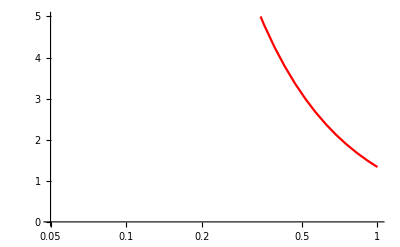
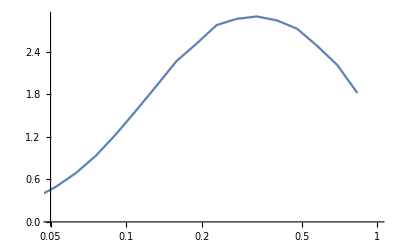
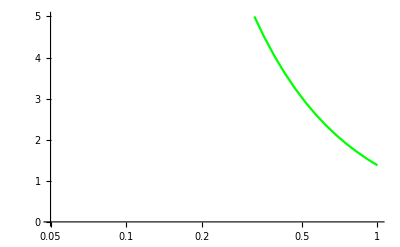
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

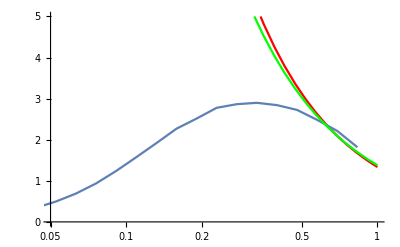

11 lines of corrupt data deleted.